# Calculado con programa en c++

```mathematica
SetDirectory["/home/pedro/Documentos/Física_Maestrias/Semestre-V/p-SCM/SCM-v1.55/test/test1"];
```

```mathematica
(*ResourceFunction["MaTeXInstall"][]*)
```

```mathematica
<<MaTeX`
```

## Datos EdS.

```mathematica
datosDeltaEdS=Import["EdS/datos-delta.dat"];
datosEdS=Import["EdS/datos-scm-parameters.dat"];
```

```mathematica
Subscript[δ, nl] = Interpolation[ Table[{datosDeltaEdS[[i,1]],datosDeltaEdS[[i,3]]},{i, 1, Length[datosDeltaEdS]}]];
Subscript[δ, l] = Interpolation[ Table[{datosDeltaEdS[[i,1]],datosDeltaEdS[[i,4]]},{i, 1, Length[datosDeltaEdS]}]];
Subscript[δ, cEdS] = Interpolation[ Table[{datosEdS[[i,1]],datosEdS[[i,3]]},{i, 1, Length[datosEdS]}]];
Subscript[g, cEdS] = Interpolation[ Table[{datosEdS[[i,1]],datosEdS[[i,4]]},{i, 1, Length[datosEdS]}]];
Subscript[ζ, cEdS] = Interpolation[ Table[{datosEdS[[i,1]],datosEdS[[i,5]]},{i, 1, Length[datosEdS]}]];
Subscript[Y, EdS] = Interpolation[ Table[{datosEdS[[i,1]],datosEdS[[i,6]]},{i, 1, Length[datosEdS]}]];
Subscript[Δ, EdS] = Interpolation[ Table[{datosEdS[[i,1]],datosEdS[[i,7]]},{i, 1, Length[datosEdS]}]];
(*Subscript[dn, cEdS] = Interpolation[ Table[{datosEdS[[i,1]],datosEdS[[i,7]]},{i, 1, Length[datosEdS]}]];
Subscript[V, cEdS] = Interpolation[ Table[{datosEdS[[i,1]],datosEdS[[i,8]]},{i, 1, Length[datosEdS]}]];
Subscript[Nbin, cEdS] = Interpolation[ Table[{datosEdS[[i,1]],datosEdS[[i,9]]},{i, 1, Length[datosEdS]}]];
Subscript[Nbin, 2cEdS] = Interpolation[ Table[{datosEdS[[i,1]],datosEdS[[i,10]]},{i, 1, Length[datosEdS]}]];
Subscript[Nbin, 3cEdS] = Interpolation[ Table[{datosEdS[[i,1]],datosEdS[[i,11]]},{i, 1, Length[datosEdS]}]];
Subscript[Nint, cEdS] = Interpolation[ Table[{datosEdS[[i,1]],datosEdS[[i,12]]},{i, 1, Length[datosEdS]}]];
Subscript[Nsi, cEdS] = Interpolation[Table[ {z, Integrate[Subscript[Nint, cEdS][x], {x, 0, z}]}, {z, 0, 10, 0.01}]];
Subscript[Nint, 2cEdS] = Interpolation[ Table[{datosEdS[[i,1]],datosEdS[[i,13]]},{i, 1, Length[datosEdS]}]];
Subscript[Nsi, 2cEdS] = Interpolation[Table[ {z, Integrate[Subscript[Nint, 2cEdS][x], {x, 0, z}]}, {z, 0, 10, 0.01}]];
Subscript[Nint, 3cEdS] = Interpolation[ Table[{datosEdS[[i,1]],datosEdS[[i,14]]},{i, 1, Length[datosEdS]}]];
Subscript[Nsi, 3cEdS] = Interpolation[Table[ {z, Integrate[Subscript[Nint, 3cEdS][x], {x, 0, z}]}, {z, 0, 10, 0.01}]];*)
```

```mathematica
{ Subscript[δ, cEdS][0], Subscript[g, cEdS][0],Subscript[ζ, cEdS][0],Subscript[Y, EdS][0],Subscript[Δ, EdS][0]}
```

{1.68636,1.,5.54969,0.5,177.644}

## Datos ΛCDM.

```mathematica
datosDeltaLCDM=Import["LCDM/datos-delta.dat"];
datosLCDMCos=Import["LCDM/cosmology.dat"];
datosLCDM=Import["LCDM/datos-scm-parameters.dat"];
datosLCDMH=Import["LCDM/datos-halos.dat"];
```

```mathematica
Subscript[δ, nlL] = Interpolation[ Table[{datosDeltaLCDM[[i,1]],datosDeltaLCDM[[i,3]]},{i, 1, Length[datosDeltaLCDM]}]];
Subscript[δ, lL] = Interpolation[ Table[{datosDeltaLCDM[[i,1]],datosDeltaLCDM[[i,4]]},{i, 1, Length[datosDeltaLCDM]}]];
Subscript[w, ΛCDM] = Interpolation[ Table[{datosLCDMCos[[i,1]],datosLCDMCos[[i,5]]},{i, 1, Length[datosLCDMCos]}]];
Subscript[δ, cΛCDM] = Interpolation[ Table[{datosLCDM[[i,1]],datosLCDM[[i,3]]},{i, 1, Length[datosLCDM]}]];
Subscript[g, cΛCDM] = Interpolation[ Table[{datosLCDM[[i,1]],datosLCDM[[i,4]]},{i, 1, Length[datosLCDM]}]];
Subscript[ζ, ΛCDM] = Interpolation[ Table[{datosLCDM[[i,1]],datosLCDM[[i,5]]},{i, 1, Length[datosLCDM]}]];
Subscript[Y, ΛCDM] = Interpolation[ Table[{datosLCDM[[i,1]],datosLCDM[[i,6]]},{i, 1, Length[datosLCDM]}]];
Subscript[Δ, ΛCDM] = Interpolation[ Table[{datosLCDM[[i,1]],datosLCDM[[i,7]]},{i, 1, Length[datosLCDM]}]];
Subscript[dn, cΛCDM] = Interpolation[ Table[{datosLCDMH[[i,1]],datosLCDMH[[i,2]]},{i, 1, Length[datosLCDMH]}]];
Subscript[V, cΛCDM] = Interpolation[ Table[{datosLCDMH[[i,1]],datosLCDMH[[i,3]]},{i, 1, Length[datosLCDMH]}]];
Subscript[Nbin, cΛCDM] = Interpolation[ Table[{datosLCDMH[[i,1]],datosLCDMH[[i,4]]},{i, 1, Length[datosLCDMH]}]];
Subscript[Nbin, 2cΛCDM] = Interpolation[ Table[{datosLCDMH[[i,1]],datosLCDMH[[i,5]]},{i, 1, Length[datosLCDMH]}]];
Subscript[Nbin, 3cΛCDM] = Interpolation[ Table[{datosLCDMH[[i,1]],datosLCDMH[[i,6]]},{i, 1, Length[datosLCDMH]}]];
Subscript[Nint, cΛCDM] = Interpolation[ Table[{datosLCDMH[[i,1]],datosLCDMH[[i,7]]},{i, 1, Length[datosLCDMH]}]];
Subscript[Nsi, cΛCDM] = Interpolation[Table[ {z, Integrate[Subscript[Nint, cΛCDM][x], {x, 0, z}]}, {z, 0, 10, 0.01}]];
Subscript[Nint, 2cΛCDM] = Interpolation[ Table[{datosLCDMH[[i,1]],datosLCDMH[[i,8]]},{i, 1, Length[datosLCDMH]}]];
Subscript[Nsi, 2cΛCDM] = Interpolation[Table[ {z, Integrate[Subscript[Nint, 2cΛCDM][x], {x, 0, z}]}, {z, 0, 10, 0.01}]];
Subscript[Nint, 3cΛCDM] = Interpolation[ Table[{datosLCDMH[[i,1]],datosLCDMH[[i,9]]},{i, 1, Length[datosLCDMH]}]];
Subscript[Nsi, 3cΛCDM] = Interpolation[Table[ {z, Integrate[Subscript[Nint, 3cΛCDM][x], {x, 0, z}]}, {z, 0, 10, 0.01}]];
```

```mathematica
{ Subscript[δ, cΛCDM][0], Subscript[g, cΛCDM][0],Subscript[ζ, ΛCDM][0],Subscript[Y, ΛCDM][0],Subscript[Δ, ΛCDM][0],Subscript[dn, cΛCDM][0],Subscript[V, cΛCDM][5],Subscript[Nbin, cΛCDM][1],Subscript[Nsi, cΛCDM][10]}
```

{1.67575,1.,6.78904,0.484921,332.909,5.0879×10^-19,3.44813×10^10,4.10819×10^7,6.10929×10^7}

## Datos neDE.

```mathematica
datosDeltaneDE=Import["neDE/datos-delta.dat"];
datosneDECos=Import["neDE/cosmology.dat"];
datosneDE=Import["neDE/datos-scm-parameters.dat"];
datosneDEH=Import["neDE/datos-halos.dat"];
```

```mathematica
Subscript[δ, nln] = Interpolation[ Table[{datosDeltaneDE[[i,1]],datosDeltaneDE[[i,3]]},{i, 1, Length[datosDeltaneDE]}]];
Subscript[δ, ln] = Interpolation[ Table[{datosDeltaneDE[[i,1]],datosDeltaneDE[[i,4]]},{i, 1, Length[datosDeltaneDE]}]];
Subscript[w, neDE] = Interpolation[ Table[{datosneDECos[[i,1]],datosneDECos[[i,5]]},{i, 1, Length[datosneDECos]}]];
Subscript[δ, cneDE] = Interpolation[ Table[{datosneDE[[i,1]],datosneDE[[i,3]]},{i, 1, Length[datosneDE]}]];
Subscript[g, cneDE] = Interpolation[ Table[{datosneDE[[i,1]],datosneDE[[i,4]]},{i, 1, Length[datosneDE]}]];
Subscript[ζ, neDE] = Interpolation[ Table[{datosneDE[[i,1]],datosneDE[[i,5]]},{i, 1, Length[datosneDE]}]];
Subscript[Y, neDE] = Interpolation[ Table[{datosneDE[[i,1]],datosneDE[[i,6]]},{i, 1, Length[datosneDE]}]];
Subscript[Δ, neDE] = Interpolation[ Table[{datosneDE[[i,1]],datosneDE[[i,7]]},{i, 1, Length[datosneDE]}]];
Subscript[dn, cneDE] = Interpolation[ Table[{datosneDEH[[i,1]],datosneDEH[[i,2]]},{i, 1, Length[datosneDEH]}]];
Subscript[V, cneDE] = Interpolation[ Table[{datosneDEH[[i,1]],datosneDEH[[i,3]]},{i, 1, Length[datosneDEH]}]];
Subscript[Nbin, cneDE] = Interpolation[ Table[{datosneDEH[[i,1]],datosneDEH[[i,4]]},{i, 1, Length[datosneDEH]}]];
Subscript[Nbin, 2cneDE] = Interpolation[ Table[{datosneDEH[[i,1]],datosneDEH[[i,5]]},{i, 1, Length[datosneDEH]}]];
Subscript[Nbin, 3cneDE] = Interpolation[ Table[{datosneDEH[[i,1]],datosneDEH[[i,6]]},{i, 1, Length[datosneDEH]}]];
Subscript[Nint, cneDE] = Interpolation[ Table[{datosneDEH[[i,1]],datosneDEH[[i,7]]},{i, 1, Length[datosneDEH]}]];
Subscript[Nsi, cneDE] = Interpolation[Table[ {z, Integrate[Subscript[Nint, cneDE][x], {x, 0, z}]}, {z, 0, 10, 0.01}]];
Subscript[Nint, 2cneDE] = Interpolation[ Table[{datosneDEH[[i,1]],datosneDEH[[i,8]]},{i, 1, Length[datosneDEH]}]];
Subscript[Nsi, 2cneDE] = Interpolation[Table[ {z, Integrate[Subscript[Nint, 2cneDE][x], {x, 0, z}]}, {z, 0, 10, 0.01}]];
Subscript[Nint, 3cneDE] = Interpolation[ Table[{datosneDEH[[i,1]],datosneDEH[[i,9]]},{i, 1, Length[datosneDEH]}]];
Subscript[Nsi, 3cneDE] = Interpolation[Table[ {z, Integrate[Subscript[Nint, 3cneDE][x], {x, 0, z}]}, {z, 0, 10, 0.01}]];
```

```mathematica
{ Subscript[δ, cneDE][0], Subscript[g, cneDE][0],Subscript[ζ, neDE][0],Subscript[Y, neDE][0],Subscript[Δ, neDE][0],Subscript[V, cneDE][10],Subscript[Nsi, cneDE][10]}
```

{1.67575,1.,6.789,0.48492,332.907,2.05235×10^10,6.10925×10^7}

```mathematica
(*FrameTicks->{{Automatic,Automatic},{Table[{10^i,DisplayForm@SuperscriptBox[10,i]},{i,-1,6,2}],Automatic}}*)
```

## Datos ESCVG.

```mathematica
datosDeltaESCVG=Import["ESCVG/datos-delta.dat"];
datosESCVGCos=Import["ESCVG/cosmology.dat"];
datosESCVG=Import["ESCVG/datos-scm-parameters.dat"];
datosESCVGH=Import["ESCVG/datos-halos.dat"];
```

```mathematica
Subscript[δ, nlCVG] = Interpolation[ Table[{datosDeltaESCVG[[i,1]],datosDeltaESCVG[[i,3]]},{i, 1, Length[datosDeltaESCVG]}]];
Subscript[δ, lCVG] = Interpolation[ Table[{datosDeltaESCVG[[i,1]],datosDeltaESCVG[[i,4]]},{i, 1, Length[datosDeltaESCVG]}]];
Subscript[w, ESCVG] = Interpolation[ Table[{datosESCVGCos[[i,1]],datosESCVGCos[[i,5]]},{i, 1, Length[datosESCVGCos]}]];
Subscript[δ, cESCVG] = Interpolation[ Table[{datosESCVG[[i,1]],datosESCVG[[i,3]]},{i, 1, Length[datosESCVG]}]];
Subscript[g, cESCVG] = Interpolation[ Table[{datosESCVG[[i,1]],datosESCVG[[i,4]]},{i, 1, Length[datosESCVG]}]];
Subscript[ζ, ESCVG] = Interpolation[ Table[{datosESCVG[[i,1]],datosESCVG[[i,5]]},{i, 1, Length[datosESCVG]}]];
Subscript[Y, ESCVG] = Interpolation[ Table[{datosESCVG[[i,1]],datosESCVG[[i,6]]},{i, 1, Length[datosESCVG]}]];
Subscript[Δ, ESCVG] = Interpolation[ Table[{datosESCVG[[i,1]],datosESCVG[[i,7]]},{i, 1, Length[datosESCVG]}]];
Subscript[dn, ESCVG] = Interpolation[ Table[{datosESCVGH[[i,1]],datosESCVGH[[i,2]]},{i, 1, Length[datosESCVGH]}]];
Subscript[V, cESCVG] = Interpolation[ Table[{datosESCVGH[[i,1]],datosESCVGH[[i,3]]},{i, 1, Length[datosESCVGH]}]];
Subscript[Nbin, cESCVG] = Interpolation[ Table[{datosESCVGH[[i,1]],datosESCVGH[[i,4]]},{i, 1, Length[datosESCVGH]}]];
Subscript[Nbin, 2cESCVG] = Interpolation[ Table[{datosESCVGH[[i,1]],datosESCVGH[[i,5]]},{i, 1, Length[datosESCVGH]}]];
Subscript[Nbin, 3cESCVG] = Interpolation[ Table[{datosESCVGH[[i,1]],datosESCVGH[[i,6]]},{i, 1, Length[datosESCVGH]}]];
Subscript[Nint, cESCVG] = Interpolation[ Table[{datosESCVGH[[i,1]],datosESCVGH[[i,7]]},{i, 1, Length[datosESCVGH]}]];
Subscript[Nsi, cESCVG] = Interpolation[Table[ {z, Integrate[Subscript[Nint, cESCVG][x], {x, 0, z}]}, {z, 0, 5, 0.01}]];
Subscript[Nint, 2cESCVG] = Interpolation[ Table[{datosESCVGH[[i,1]],datosESCVGH[[i,8]]},{i, 1, Length[datosESCVGH]}]];
Subscript[Nsi, 2cESCVG] = Interpolation[Table[ {z, Integrate[Subscript[Nint, 2cESCVG][x], {x, 0, z}]}, {z, 0, 5, 0.01}]];
Subscript[Nint, 3cESCVG] = Interpolation[ Table[{datosESCVGH[[i,1]],datosESCVGH[[i,9]]},{i, 1, Length[datosESCVGH]}]];
Subscript[Nsi, 3cESCVG] = Interpolation[Table[ {z, Integrate[Subscript[Nint, 3cESCVG][x], {x, 0, z}]}, {z, 0, 5, 0.01}]];
```

```mathematica
{ Subscript[δ, cESCVG][0], Subscript[g, cESCVG][0],Subscript[ζ, ESCVG][0],Subscript[Y, ESCVG][0],Subscript[Δ, ESCVG][0],Subscript[Nsi, cESCVG][4]}
```

{1.67591,1.,6.75913,0.485276,328.293,6.18924×10^7}

```mathematica
(*FrameTicks->{{Automatic,Automatic},{Table[{10^i,DisplayForm@SuperscriptBox[10,i]},{i,-1,6,2}],Automatic}}*)
```

## Datos 2Formas.

```mathematica
datos2FORMCos=Import["2FORM/cosmology.dat"];
datos2FORM=Import["2FORM/datos-scm-parameters.dat"];
datos2FORMH=Import["2FORM/datos-halos.dat"];
```

```mathematica
Subscript[w, 2FORM] = Interpolation[ Table[{datos2FORMCos[[i,1]],datos2FORMCos[[i,5]]},{i, 1, Length[datos2FORMCos]}]];
Subscript[δ, c2FORM] = Interpolation[ Table[{datos2FORM[[i,1]],datos2FORM[[i,3]]},{i, 1, Length[datos2FORM]}]];
Subscript[g, c2FORM] = Interpolation[ Table[{datos2FORM[[i,1]],datos2FORM[[i,4]]},{i, 1, Length[datos2FORM]}]];
Subscript[ζ, 2FORM] = Interpolation[ Table[{datos2FORM[[i,1]],datos2FORM[[i,5]]},{i, 1, Length[datos2FORM]}]];
Subscript[Y, 2FORM] = Interpolation[ Table[{datos2FORM[[i,1]],datos2FORM[[i,6]]},{i, 1, Length[datos2FORM]}]];
Subscript[Δ, 2FORM] = Interpolation[ Table[{datos2FORM[[i,1]],datos2FORM[[i,7]]},{i, 1, Length[datos2FORM]}]];
Subscript[dn, 2FORM] = Interpolation[ Table[{datos2FORMH[[i,1]],datos2FORMH[[i,2]]},{i, 1, Length[datos2FORMH]}]];
Subscript[V, c2FORM] = Interpolation[ Table[{datos2FORMH[[i,1]],datos2FORMH[[i,3]]},{i, 1, Length[datos2FORMH]}]];
Subscript[Nbin, c2FORM] = Interpolation[ Table[{datos2FORMH[[i,1]],datos2FORMH[[i,4]]},{i, 1, Length[datos2FORMH]}]];
Subscript[Nbin, 2c2FORM] = Interpolation[ Table[{datos2FORMH[[i,1]],datos2FORMH[[i,5]]},{i, 1, Length[datos2FORMH]}]];
Subscript[Nbin, 3c2FORM] = Interpolation[ Table[{datos2FORMH[[i,1]],datos2FORMH[[i,6]]},{i, 1, Length[datos2FORMH]}]];
Subscript[Nint, c2FORM] = Interpolation[ Table[{datos2FORMH[[i,1]],datos2FORMH[[i,7]]},{i, 1, Length[datos2FORMH]}]];
Subscript[Nsi, c2FORM] = Interpolation[Table[ {z, Integrate[Subscript[Nint, c2FORM][x], {x, 0, z}]}, {z, 0, 5, 0.01}]];
Subscript[Nint, 2c2FORM] = Interpolation[ Table[{datos2FORMH[[i,1]],datos2FORMH[[i,8]]},{i, 1, Length[datos2FORMH]}]];
Subscript[Nsi, 2c2FORM] = Interpolation[Table[ {z, Integrate[Subscript[Nint, 2c2FORM][x], {x, 0, z}]}, {z, 0, 5, 0.01}]];
Subscript[Nint, 3c2FORM] = Interpolation[ Table[{datos2FORMH[[i,1]],datos2FORMH[[i,9]]},{i, 1, Length[datos2FORMH]}]];
Subscript[Nsi, 3c2FORM] = Interpolation[Table[ {z, Integrate[Subscript[Nint, 3c2FORM][x], {x, 0, z}]}, {z, 0, 5, 0.01}]];
```

```mathematica
{ Subscript[δ, c2FORM][0], Subscript[g, c2FORM][0],Subscript[ζ, 2FORM][0],Subscript[Y, 2FORM][0],Subscript[Δ, 2FORM][0],Subscript[Nsi, c2FORM][4]}
```

{1.67587,1.,6.76989,0.485534,324.716,5.81732×10^7}

## Datos No Abeliano.

```mathematica
datosNonAbelianCos=Import["NonAbelian/cosmology.dat"];
datosNonAbelian=Import["NonAbelian/datos-scm-parameters.dat"];
datosNonAbelianH=Import["NonAbelian/datos-halos.dat"];
```

```mathematica
Subscript[w, NA] = Interpolation[ Table[{datosNonAbelianCos[[i,1]],datosNonAbelianCos[[i,5]]},{i, 1, Length[datosNonAbelianCos]}]];
Subscript[δ, cNA] = Interpolation[ Table[{datosNonAbelian[[i,1]],datosNonAbelian[[i,3]]},{i, 1, Length[datosNonAbelian]}]];
Subscript[g, cNA] = Interpolation[ Table[{datosNonAbelian[[i,1]],datosNonAbelian[[i,4]]},{i, 1, Length[datosNonAbelian]}]];
Subscript[ζ, NA] = Interpolation[ Table[{datosNonAbelian[[i,1]],datosNonAbelian[[i,5]]},{i, 1, Length[datosNonAbelian]}]];
Subscript[Y, NA] = Interpolation[ Table[{datosNonAbelian[[i,1]],datosNonAbelian[[i,6]]},{i, 1, Length[datosNonAbelian]}]];
Subscript[Δ, NA] = Interpolation[ Table[{datosNonAbelian[[i,1]],datosNonAbelian[[i,7]]},{i, 1, Length[datosNonAbelian]}]];
Subscript[dn, NA] = Interpolation[ Table[{datosNonAbelianH[[i,1]],datosNonAbelianH[[i,2]]},{i, 1, Length[datosNonAbelianH]}]];
Subscript[V, cNA] = Interpolation[ Table[{datosNonAbelianH[[i,1]],datosNonAbelianH[[i,3]]},{i, 1, Length[datosNonAbelianH]}]];
Subscript[Nbin, cNA] = Interpolation[ Table[{datosNonAbelianH[[i,1]],datosNonAbelianH[[i,4]]},{i, 1, Length[datosNonAbelianH]}]];
Subscript[Nbin, 2cNA] = Interpolation[ Table[{datosNonAbelianH[[i,1]],datosNonAbelianH[[i,5]]},{i, 1, Length[datosNonAbelianH]}]];
Subscript[Nbin, 3cNA] = Interpolation[ Table[{datosNonAbelianH[[i,1]],datosNonAbelianH[[i,6]]},{i, 1, Length[datosNonAbelianH]}]];
Subscript[Nint, cNA] = Interpolation[ Table[{datosNonAbelianH[[i,1]],datosNonAbelianH[[i,7]]},{i, 1, Length[datosNonAbelianH]}]];
Subscript[Nsi, cNA] = Interpolation[Table[ {z, Integrate[Subscript[Nint, cNA][x], {x, 0, z}]}, {z, 0, 5, 0.01}]];
Subscript[Nint, 2cNA] = Interpolation[ Table[{datosNonAbelianH[[i,1]],datosNonAbelianH[[i,8]]},{i, 1, Length[datosNonAbelianH]}]];
Subscript[Nsi, 2cNA] = Interpolation[Table[ {z, Integrate[Subscript[Nint, 2cNA][x], {x, 0, z}]}, {z, 0, 5, 0.01}]];
Subscript[Nint, 3cNA] = Interpolation[ Table[{datosNonAbelianH[[i,1]],datosNonAbelianH[[i,9]]},{i, 1, Length[datosNonAbelianH]}]];
Subscript[Nsi, 3cNA] = Interpolation[Table[ {z, Integrate[Subscript[Nint, 3cNA][x], {x, 0, z}]}, {z, 0, 5, 0.01}]];
```

```mathematica
{ Subscript[δ, cNA][0], Subscript[g, cNA][0],Subscript[ζ, NA][0],Subscript[Y, NA][0],Subscript[Δ, NA][0],Subscript[V, cNA][1],Subscript[Nsi, cNA][3]}
```

{1.67554,1.,6.81787,0.484664,336.667,2.93705×10^10,6.19573×10^7}

## Sobredensidad no lineal

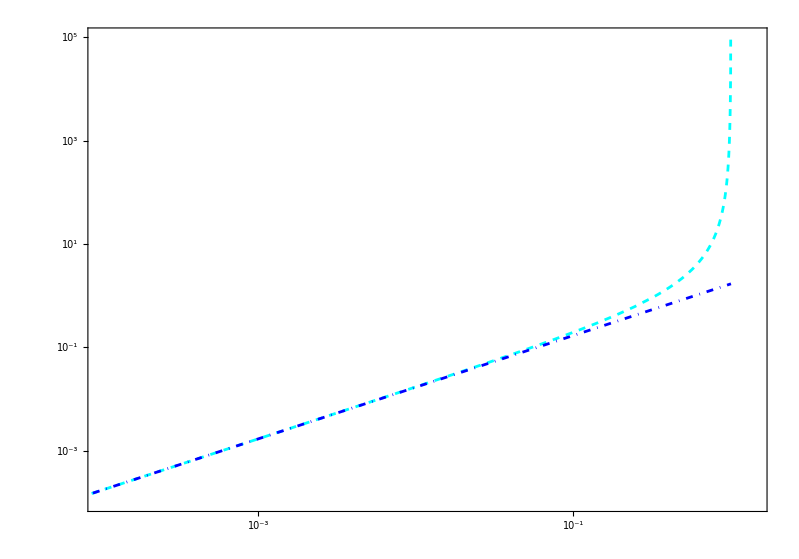

```mathematica
Plot[{Subscript[δ, nl][a], Subscript[δ, l][a](*,Subscript[δ, nlL][a], Subscript[δ, nln][a], Subscript[δ, nlCVG][a]*)}, {a,1,10^-6}, 
PlotRange->{{10^-4,1.4},{10^-4,10^5}},
Frame->True,Axes->False,FrameTicks->{{Table[{10^i,DisplayForm@SuperscriptBox[10,i]},{i,-5,6,2}],Automatic},{Table[{10^i,DisplayForm@SuperscriptBox[10,i]},{i,-5,6,1}],Automatic}},
ImageSize->5*350/3.54*{GoldenRatio,1},AspectRatio->0.7,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->18, Bold}, ScalingFunctions->{"Log","Log"},
FrameLabel->(MaTeX[#,Magnification->3]&)/@{"\\boldsymbol{a}", "\\boldsymbol{\\delta(a)}"},
PlotStyle->{ Directive[ Cyan, Dashed],
Directive[ Blue, DotDashed](*, 
Directive[ Purple, Dashed], 
Directive[Orange, DotDashed](*, 
Directive[ Red]*)*)}, 
PlotLegends->Placed[LineLegend[{
Directive[ Cyan, Dashed],
Directive[ Blue, DotDashed](*,
Directive[ Purple, Dashed], 
Directive[ Orange, DotDashed](*,
Directive[ Red]*)*)}, 
{(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{\\delta \\ No \\ Lineal}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{\\delta \\ Lineal}"](*,
(MaTeX[#,Magnification->1.3]&)/@Style["neDE"], 
(MaTeX[#,Magnification->1.3]&)/@Style["EOCVG"](*,
(MaTeX[#,Magnification->1.3]&)/@Style["2FORM"]*)*)}, 
LegendMarkerSize->30,LegendFunction->(Framed[#,RoundingRadius->10,FrameStyle->LightGray]&), LegendLayout->{"Column",1},LabelStyle->{Black,12}],{{0.03,0.73},{0,0}}](*, Epilog-> Inset[Plot[Subscript[w, 2F][a],{a, 0.01,10^7}, Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},FrameTicks->None,PlotRange->{{0.01,10},{-1.,-0.94}}],{1,-0.4}]*)]
```

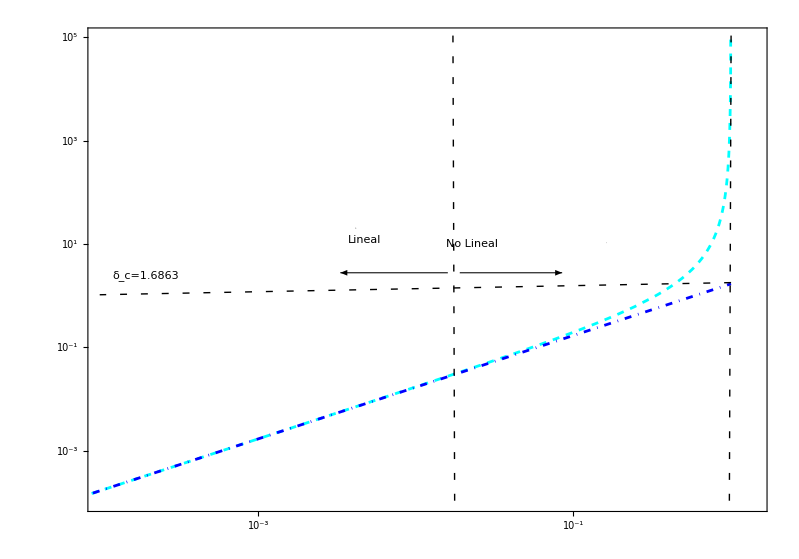

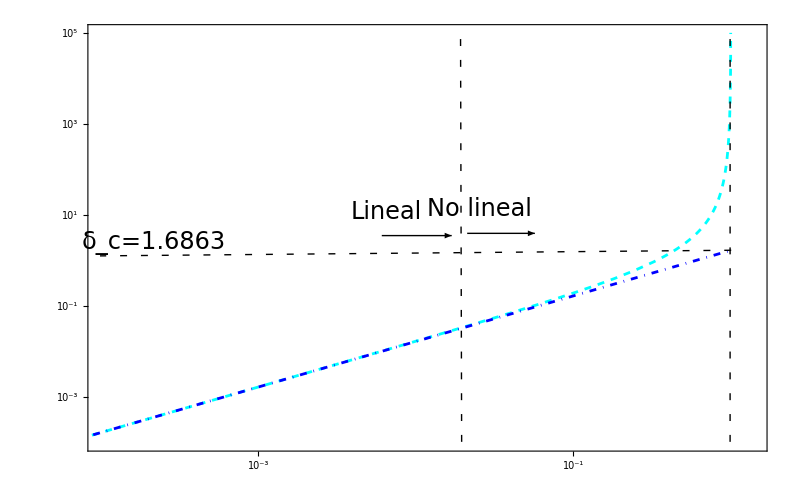

## Sobredensidad lineal

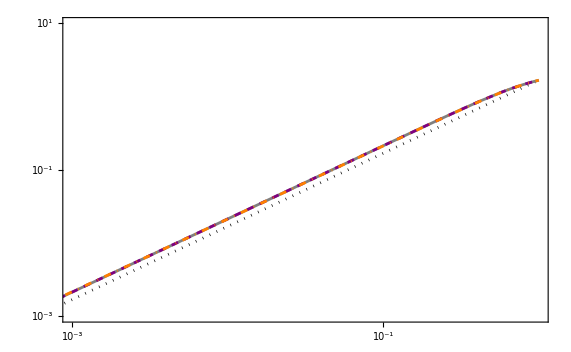

```mathematica
Plot[{Subscript[δ, l][a],Subscript[δ, lL][a], Subscript[δ, ln][a], Subscript[δ, lCVG][a]}, {a,1,10^-6}, 
PlotRange->{{10^-3,1.},{10^-3,10^1}},
Frame->True,Axes->False,FrameTicks->{{Table[{10^i,DisplayForm@SuperscriptBox[10,i]},{i,-5,6,2}],Automatic},{Table[{10^i,DisplayForm@SuperscriptBox[10,i]},{i,-5,6,1}],Automatic}},
ImageSize->5*250/3.54*{GoldenRatio,1},FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->18}, ScalingFunctions->{"Log","Log"},
FrameLabel->(MaTeX[#,Magnification->1.7]&)/@{"z +1", "w(z)"},
PlotStyle->{ Directive[ Black, Dotted],
Directive[ Gray], 
Directive[ Purple, Dashed], 
Directive[Orange, DotDashed](*, 
Directive[ Red]*)}, 
PlotLegends->Placed[LineLegend[{
Directive[ Black, Dotted],
Directive[ Gray],
Directive[ Purple, Dashed], 
Directive[ Orange, DotDashed](*,
Directive[ Red]*)}, 
{(MaTeX[#,Magnification->1.3]&)/@Style["EdS"],
(MaTeX[#,Magnification->1.3]&)/@Style["\\Lambda CDM"],
(MaTeX[#,Magnification->1.3]&)/@Style["neDE"], 
(MaTeX[#,Magnification->1.3]&)/@Style["EOCVG"](*,
(MaTeX[#,Magnification->1.3]&)/@Style["2FORM"]*)}, 
LegendMarkerSize->25,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&), LegendLayout->{"Column",2},LabelStyle->{Black,Bold,12}],{{0.03,0.65},{0,0}}](*, Epilog-> Inset[Plot[Subscript[w, 2F][a],{a, 0.01,10^7}, Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},FrameTicks->None,PlotRange->{{0.01,10},{-1.,-0.94}}],{1,-0.4}]*)]
```

## Ecuación de estado

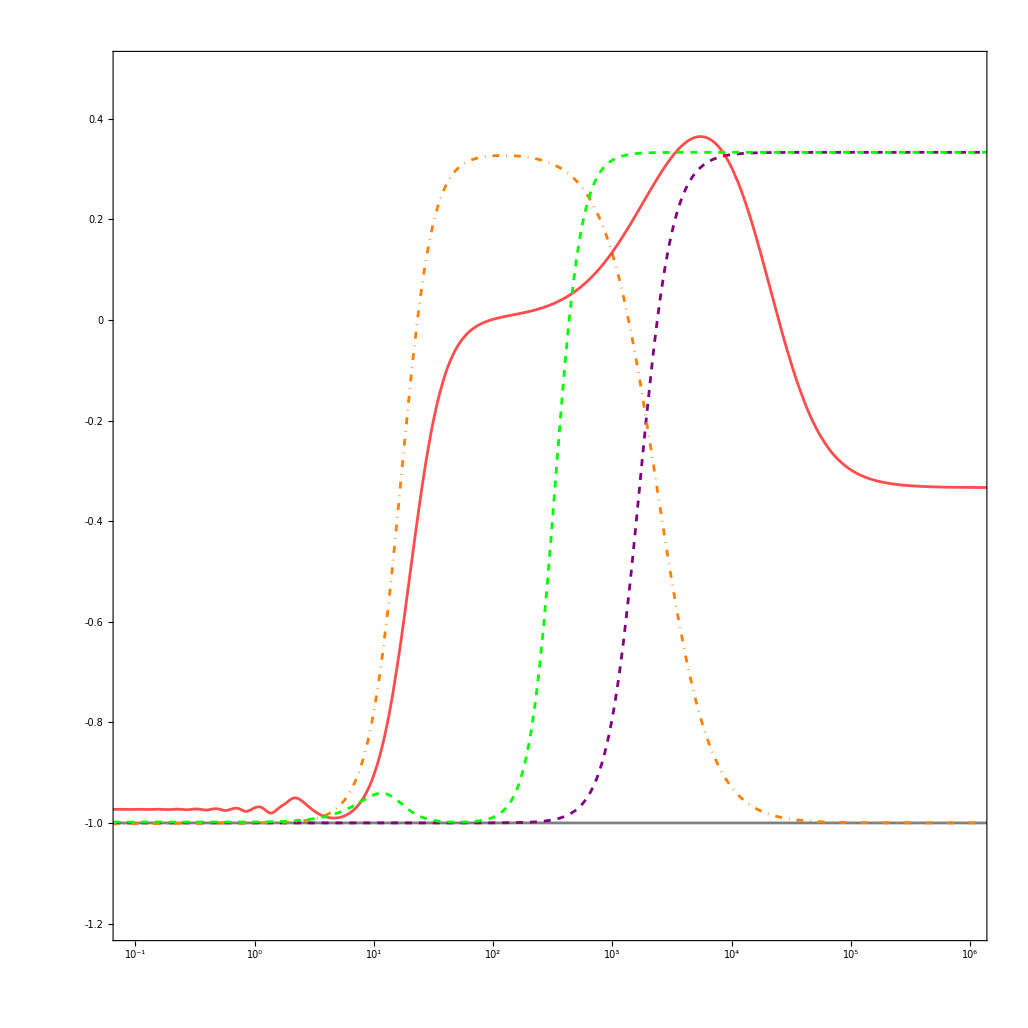

```mathematica
eos=Plot[{Subscript[w, ΛCDM][z], Subscript[w, neDE][z],Subscript[w, ESCVG][z],Subscript[w, 2FORM][z], Subscript[w, NA][z]}, {z,0.01,10^7}, 
PlotRange->{{0.09,10^6},{-1.2,0.5}},
Frame->True,Axes->False,FrameTicks->{{Automatic,Automatic},{Table[{10^i,DisplayForm@SuperscriptBox[10,i]},{i,-1,6,1}],Automatic}},
ImageSize->5*450/3.54*{GoldenRatio,1},AspectRatio->1,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->18, Bold}, ScalingFunctions->{"Log","Linear"},
FrameLabel->(MaTeX[#,Magnification->3]&)/@{"\\boldsymbol{z +1}", "\\boldsymbol{w_{_{DE}}(z)}"},
PlotStyle->{ Directive[ Medium,Gray], 
Directive[ Purple, Dashed], 
Directive[Orange, DotDashed], 
Directive[ Medium,Red, Opacity[0.7]], 
Directive[ Green, Dashing[Small]]}, 
PlotLegends->Placed[LineLegend[{
Directive[Medium, Gray],
Directive[ Purple, Dashed], 
Directive[ Orange, DotDashed],
Directive[ Medium,Red, Opacity[0.7]],
Directive[ Green, Dashing[Small]]}, 
{(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{\\Lambda CDM}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{neDE}"], 
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{EOCVG}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{2FORM}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{NA}"]}, 
LegendMarkerSize->30,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&), LegendLayout->{"Column",1},LabelStyle->{Black,Bold,15}],{{0.03,0.55},{0,0}}](*, Epilog-> Inset[Plot[{Subscript[w, ΛCDM][z],Subscript[w, neDE][z],Subscript[w, ESCVG][z],Subscript[w, 2FORM][z], Subscript[w, NA][z]},{z, 0.01,10^7}, Frame->True,Axes->False,ScalingFunctions->{"Log","Linear"},FrameTicks->None,PlotRange->{{0.09,10^2},{-1.005,-0.94}}],{1,-0.5}]*)]
```

```mathematica
ampeos=Plot[{Subscript[w, ΛCDM][z], Subscript[w, neDE][z],Subscript[w, ESCVG][z],Subscript[w, 2FORM][z], Subscript[w, NA][z]}, {z,0.01,10^7}, 
PlotRange->{{0.09,10^2},{-1.005,-0.94}},
Frame->True,Axes->False,FrameTicks->{{Automatic,Automatic},{Table[{10^i,DisplayForm@SuperscriptBox[10,i]},{i,-1,6,1}],Automatic}},
ImageSize->5*450/3.54*{GoldenRatio,1},AspectRatio->1,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->18}, ScalingFunctions->{"Log","Linear"},
FrameLabel->(MaTeX[#,Magnification->1.7]&)/@{"z +1", "w_{_{DE}}(z)"},
PlotStyle->{ Directive[ Medium,Gray], 
Directive[ Purple, Dashed], 
Directive[Orange, DotDashed], 
Directive[ Medium,Red, Opacity[0.7]], 
Directive[ Green, Dashing[Small]]}, 
PlotLegends->Placed[LineLegend[{
Directive[Medium, Gray],
Directive[ Purple, Dashed], 
Directive[ Orange, DotDashed],
Directive[ Medium,Red, Opacity[0.7]],
Directive[ Green, Dashing[Small]]}, 
{(MaTeX[#,Magnification->1.3]&)/@Style["\\Lambda CDM"],
(MaTeX[#,Magnification->1.3]&)/@Style["neDE"], 
(MaTeX[#,Magnification->1.3]&)/@Style["EOCVG"],
(MaTeX[#,Magnification->1.3]&)/@Style["2FORM"],
(MaTeX[#,Magnification->1.3]&)/@Style["NA"]}, 
LegendMarkerSize->25,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&), LegendLayout->{"Column",1},LabelStyle->{Black,Bold,12}],{{0.03,0.65},{0,0}}]];
```

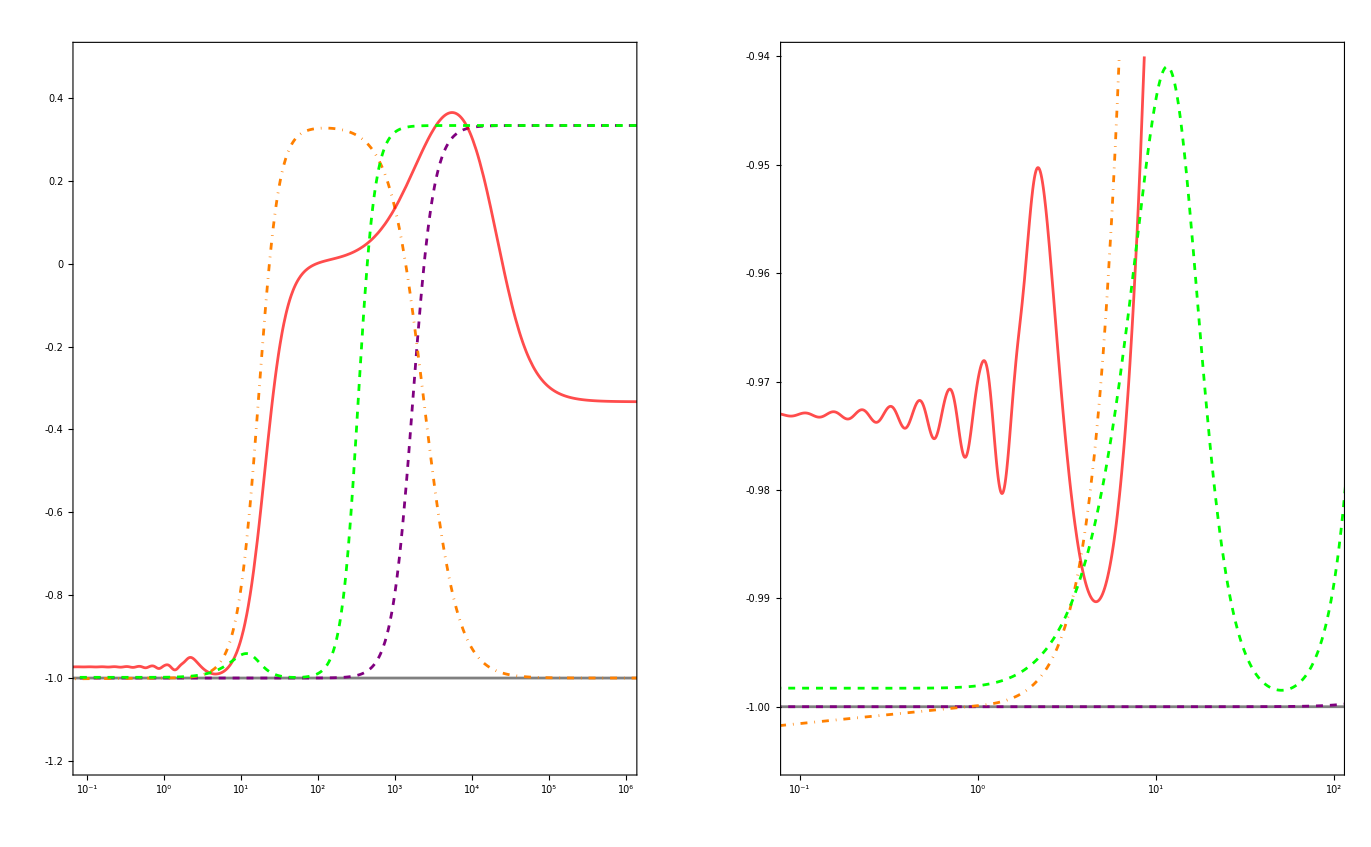

```mathematica
GraphicsGrid[{{eos, ampeos}},ImageSize->5*600/3.54*{GoldenRatio,1},AspectRatio->1]
```

## Densidad crítica

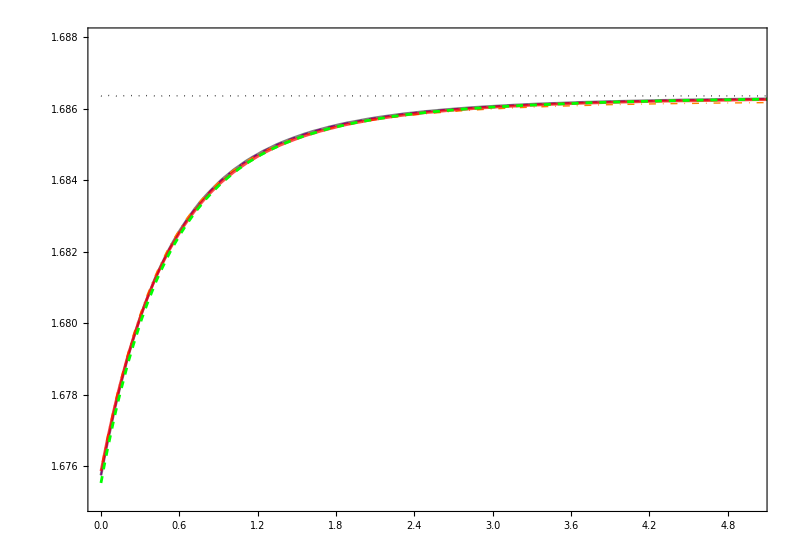

```mathematica
Plot[{ Subscript[δ, cEdS][z],Subscript[δ, cΛCDM][z], Subscript[δ, cneDE][z], Subscript[δ, cESCVG][z], Subscript[δ, c2FORM][z], Subscript[δ, cNA][z]}, {z,0,10},
Frame->True,Axes->False, ImageSize->5*350/3.54*{GoldenRatio,1},AspectRatio->0.7,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->18, Bold},FrameLabel->(MaTeX[#,Magnification->3]&)/@{"\\boldsymbol{z}", "\\boldsymbol{\\delta_{c}(z)}"}, 
PlotStyle->{ Directive[Thick, Black, Dotted],
Directive[Medium,Gray], 
Directive[Thick, Purple, Dashed], 
Directive[Thick, Orange, DotDashed], 
Directive[ Medium,Red, Opacity[0.7]], 
Directive[ Green, Dashing[Small]]}, 
PlotRange->{{0, 5},{1.675, 1.688}}, 
PlotLegends->Placed[LineLegend[{
Directive[Thick, Black, Dotted],
Directive[Medium,Gray],
Directive[Thick, Purple, Dashed],
Directive[Thick, Orange, DotDashed],
Directive[ Medium,Red, Opacity[0.7]],
Directive[ Green, Dashing[Small]]}, 
{(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{EdS}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{\\Lambda CDM}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{neDE}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{EOCVG}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{2FORM}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{NA}"]}, 
LegendMarkerSize->30,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&), LegendLayout->{"Column",1},LabelStyle->{Black,Bold,15}],{{0.72,0.04},{0,0}}](*, Epilog-> Inset[Plot[{Subscript[δ, cEdS][z],Subscript[δ, cΛCDM][z], Subscript[δ, cneDE][z], Subscript[δ, cESCVG][z], Subscript[δ, c2FORM][z], Subscript[δ, cNA][z]},{z, 0,10}, Frame->True,ImageSize->5*100/3.54*{GoldenRatio,1},Axes->False,FrameTicks->None,PlotRange->{{4,5},{1.6856,1.68647}},PlotStyle->{ Directive[Thick, Black, Dotted],Directive[Medium,Gray], Directive[Thick, Purple, Dashed], Directive[Thick, Orange, DotDashed], Directive[ Medium,Red, Opacity[0.7]], Directive[ Green, Dashing[Small]]}],{4.2,1.684}]*)]
```

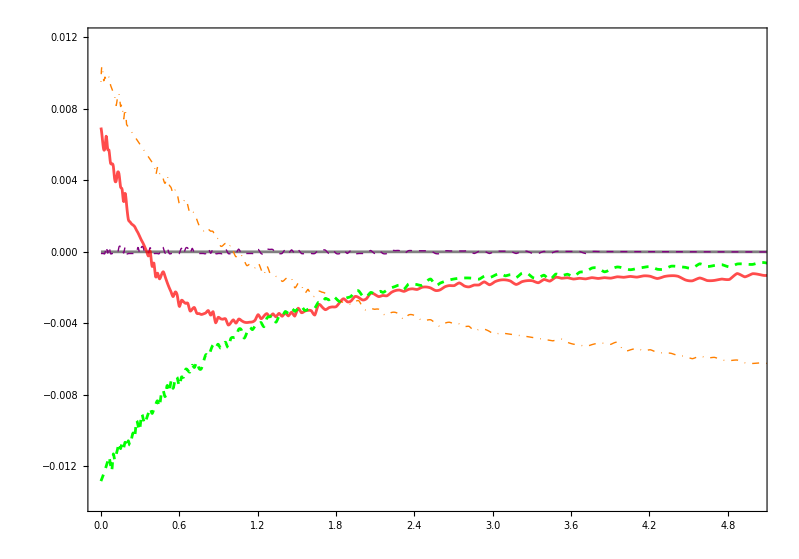

```mathematica
Plot[{(( Subscript[δ, cΛCDM][z]-Subscript[δ, cΛCDM][z])/Subscript[δ, cΛCDM][z])*100, (((Subscript[δ, cneDE][z]-Subscript[δ, cΛCDM][z])/Subscript[δ, cΛCDM][z])/Subscript[δ, cΛCDM][z])*100, ((Subscript[δ, cESCVG][z]-Subscript[δ, cΛCDM][z])/Subscript[δ, cΛCDM][z])*100, ((Subscript[δ, c2FORM][z]-Subscript[δ, cΛCDM][z])/Subscript[δ, cΛCDM][z])*100, ((Subscript[δ, cNA][z]-Subscript[δ, cΛCDM][z])/Subscript[δ, cΛCDM][z])*100}, {z,0,10},
Frame->True,Axes->False, ImageSize->5*350/3.54*{GoldenRatio,1},AspectRatio->0.7,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->18, Bold},FrameLabel->(MaTeX[#,Magnification->3]&)/@{"\\boldsymbol{z}", "\\boldsymbol{\\Delta \\delta_{c}(\\%)}"}, 
PlotStyle->{ 
Directive[Medium,Gray], 
Directive[Thick, Purple, Dashed], 
Directive[Thick, Orange, DotDashed], 
Directive[ Medium,Red, Opacity[0.7]], 
Directive[ Green, Dashing[Small]]}, 
PlotRange->{{0, 5},{-0.014, 0.012}}]
```

## Factor de crecimiento, normalizado al factor de escala.

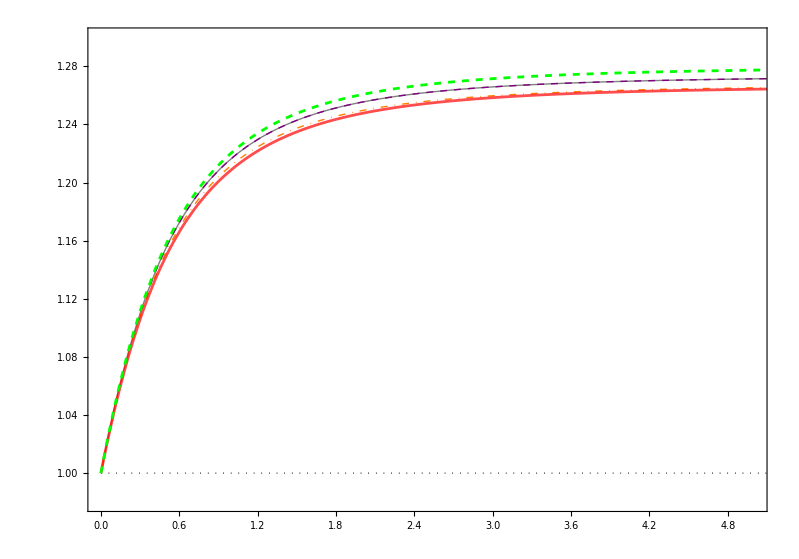

```mathematica
Plot[{ Subscript[g, cEdS][z],Subscript[g, cΛCDM][z], Subscript[g, cneDE][z], Subscript[g, cESCVG][z], Subscript[g, c2FORM][z], Subscript[g, cNA][z]}, {z,0,10},
Frame->True,Axes->False, ImageSize->5*350/3.54*{GoldenRatio,1}, AspectRatio->0.7,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->18, Bold},FrameLabel->(MaTeX[#,Magnification->3]&)/@{"\\boldsymbol{z}", "\\boldsymbol{D_{+}(a)/a}"}, 
PlotStyle->{ Directive[Thick, Black, Dotted], 
Directive[Thick, Gray], 
Directive[Thick, Purple, Dashed], 
Directive[Thick, Orange, DotDashed], 
Directive[ Medium,Red, Opacity[0.7]], 
Directive[ Green, Dashing[Small]]}, 
PlotRange->{{0, 5},{0.98, 1.3}}, 
PlotLegends->Placed[LineLegend[{
Directive[Thick, Black, Dotted],
Directive[Thick, Gray],
Directive[Thick, Purple, Dashed],
Directive[Thick, Orange, DotDashed],
Directive[ Medium,Red, Opacity[0.7]],
Directive[ Green, Dashing[Small]]}, 
{(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{EdS}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{\\Lambda CDM}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{neDE}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{EOCVG}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{2FORM}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{NA}"]}, 
LegendMarkerSize->30,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&), LegendLayout->{"Column",2},LabelStyle->{Black,Bold,15}],{{0.5,0.1},{0,0}}]]
```

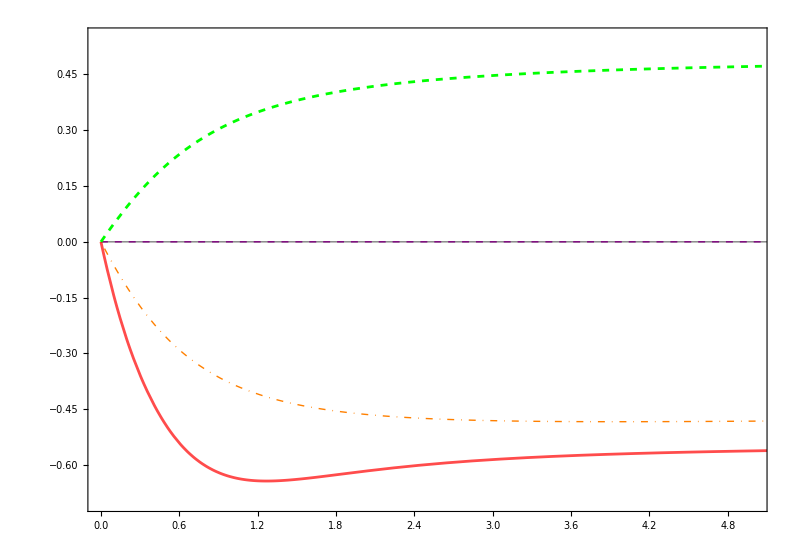

```mathematica
Plot[{((Subscript[g, cΛCDM][z]-Subscript[g, cΛCDM][z])/Subscript[g, cΛCDM][z])*100,((Subscript[g, cneDE][z]-Subscript[g, cΛCDM][z])/Subscript[g, cΛCDM][z])*100, ((Subscript[g, cESCVG][z]-Subscript[g, cΛCDM][z])/Subscript[g, cΛCDM][z])*100, ((Subscript[g, c2FORM][z]-Subscript[g, cΛCDM][z])/Subscript[g, cΛCDM][z])*100, ((Subscript[g, cNA][z]-Subscript[g, cΛCDM][z])/Subscript[g, cΛCDM][z])*100}, {z,0,10},
Frame->True,Axes->False, ImageSize->5*350/3.54*{GoldenRatio,1}, AspectRatio->0.7,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->18, Bold},FrameLabel->(MaTeX[#,Magnification->3]&)/@{"\\boldsymbol{z}", "\\boldsymbol{\\Delta D_{+}(a)/a (\\%)}"}, 
PlotStyle->{  
Directive[Thick, Gray], 
Directive[Thick, Purple, Dashed], 
Directive[Thick, Orange, DotDashed], 
Directive[ Medium,Red, Opacity[0.7]], 
Directive[ Green, Dashing[Small]]}, 
PlotRange->{{0, 5},{-0.7, 0.55}}]
```

## Densidad no lineal en el giro.

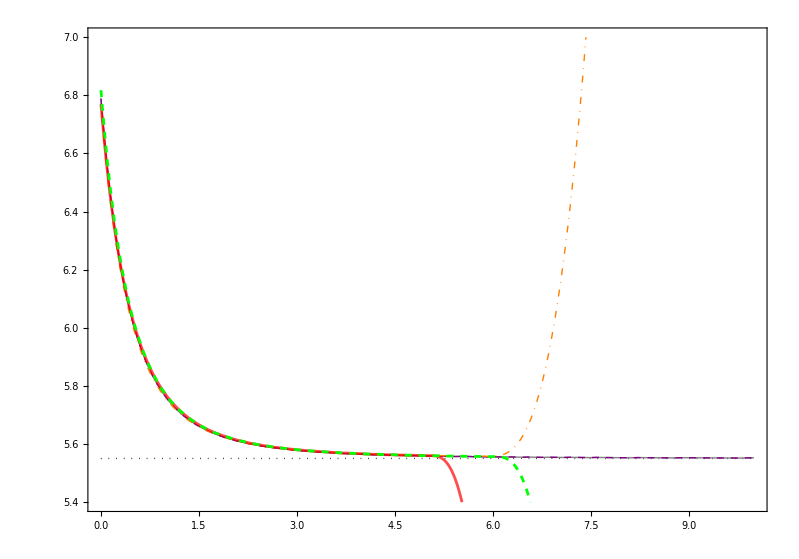

```mathematica
Plot[{Subscript[ζ, cEdS][z], Subscript[ζ, ΛCDM][z], Subscript[ζ, neDE][z], Subscript[ζ, ESCVG][z], Subscript[ζ, 2FORM][z],Subscript[ζ, NA][z]}, {z,0,10},
Frame->True,Axes->False, ImageSize->5*350/3.54*{GoldenRatio,1}, AspectRatio->0.7,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->18, Bold},FrameLabel->(MaTeX[#,Magnification->3]&)/@{"\\boldsymbol{z}", "\\boldsymbol{\\zeta (z)}"}, 
PlotStyle->{ Directive[Thick, Black, Dotted], 
Directive[Thick, Gray], 
Directive[Thick, Purple, Dashed], 
Directive[Thick, Orange, DotDashed], 
Directive[ Medium,Red, Opacity[0.7]], 
Directive[ Green, Dashing[Small]]}, 
PlotRange->{{0, 3},{7, 5.4}}, 
PlotLegends->Placed[LineLegend[{
Directive[Thick, Black, Dotted],
Directive[Thick, Gray],
Directive[Thick, Purple, Dashed],
Directive[Thick, Orange, DotDashed],
Directive[ Medium,Red, Opacity[0.7]],
Directive[ Green, Dashing[Small]]}, 
{(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{EdS}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{\\Lambda CDM}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{neDE}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{EOCVG}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{2FORM}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{NA}"]}, 
LegendMarkerSize->30,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&), LegendLayout->{"Column",1},LabelStyle->{Black,Bold,15}],{{0.72,0.3},{0,0}}]]
```

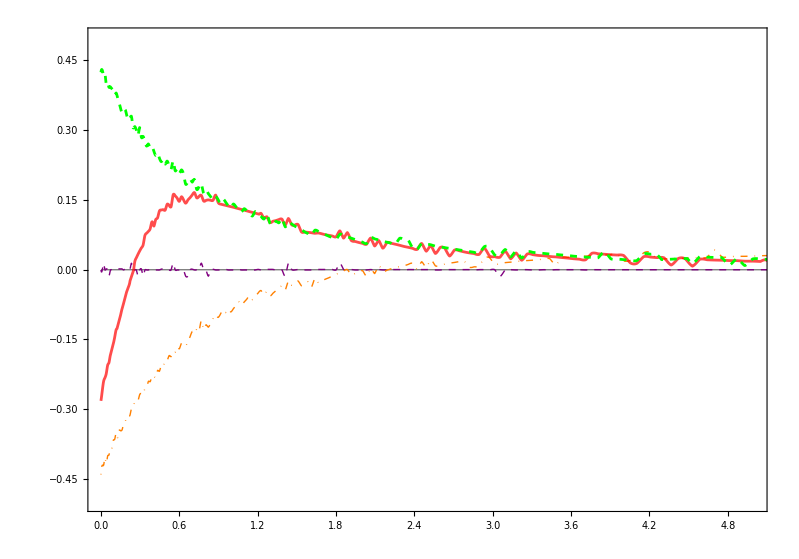

```mathematica
Plot[{((Subscript[ζ, ΛCDM][z]-Subscript[ζ, ΛCDM][z])/Subscript[ζ, ΛCDM][z])*100,(( Subscript[ζ, neDE][z]-Subscript[ζ, ΛCDM][z])/Subscript[ζ, ΛCDM][z])*100,(( Subscript[ζ, ESCVG][z]-Subscript[ζ, ΛCDM][z])/Subscript[ζ, ΛCDM][z])*100,(( Subscript[ζ, 2FORM][z]-Subscript[ζ, ΛCDM][z])/Subscript[ζ, ΛCDM][z])*100,((Subscript[ζ, NA][z]-Subscript[ζ, ΛCDM][z])/Subscript[ζ, ΛCDM][z])*100}, {z,0,10},
Frame->True,Axes->False, ImageSize->5*350/3.54*{GoldenRatio,1}, AspectRatio->0.7,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->18, Bold},FrameLabel->(MaTeX[#,Magnification->3]&)/@{"\\boldsymbol{z}", "\\boldsymbol{\\Delta \\zeta (\\%)}"}, 
PlotStyle->{ 
Directive[Thick, Gray], 
Directive[Thick, Purple, Dashed], 
Directive[Thick, Orange, DotDashed], 
Directive[ Medium,Red, Opacity[0.7]], 
Directive[ Green, Dashing[Small]]}, 
PlotRange->{{0, 5},{-0.5, 0.5}}]
```

## Radio virializado.

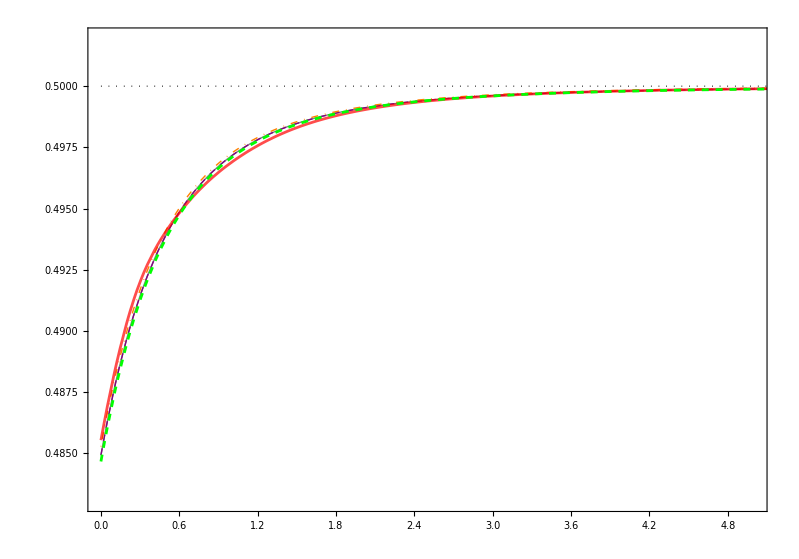

```mathematica
Plot[{Subscript[Y, EdS][z], Subscript[Y, ΛCDM][z], Subscript[Y, neDE][z], Subscript[Y, ESCVG][z],Subscript[Y, 2FORM][z], Subscript[Y, NA][z]}, {z,0,10},
Frame->True,Axes->False, ImageSize->5*350/3.54*{GoldenRatio,1}, AspectRatio->0.7,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->18, Bold},FrameLabel->(MaTeX[#,Magnification->3]&)/@{"\\boldsymbol{z}", "\\boldsymbol{y_{_{vir}}(z)}"}, 
PlotStyle->{ Directive[Thick, Black, Dotted], 
Directive[Thick, Gray], 
Directive[Thick, Purple, Dashed], 
Directive[Thick, Orange, DotDashed], 
Directive[ Medium,Red, Opacity[0.7]], 
Directive[ Green, Dashing[Small]]}, 
PlotRange->{{0, 5},{0.483, 0.502}}, 
PlotLegends->Placed[LineLegend[{
Directive[Thick, Black, Dotted],
Directive[Thick, Gray],
Directive[Thick, Purple, Dashed],
Directive[Thick, Orange, DotDashed], 
Directive[ Medium,Red, Opacity[0.7]],
Directive[ Green, Dashing[Small]]}, 
{(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{EdS}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{\\Lambda CDM}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{neDE}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{EOCVG}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{2FORM}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{NA}"]}, 
LegendMarkerSize->30,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&), LegendLayout->{"Column",1},LabelStyle->{Black,Bold,15}],{{0.72,0.05},{0,0}}]]
```

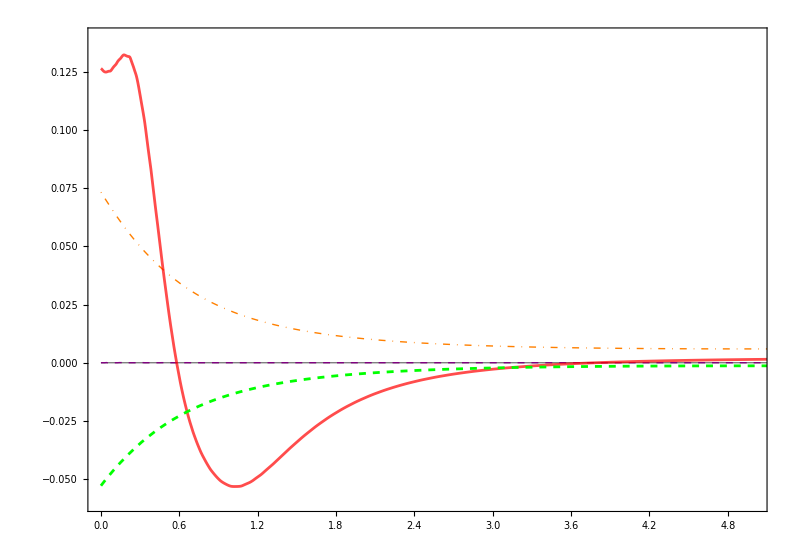

```mathematica
Plot[{(( Subscript[Y, ΛCDM][z]-Subscript[Y, ΛCDM][z])/Subscript[Y, ΛCDM][z])*100,(( Subscript[Y, neDE][z]-Subscript[Y, ΛCDM][z])/Subscript[Y, ΛCDM][z])*100, ((Subscript[Y, ESCVG][z]-Subscript[Y, ΛCDM][z])/Subscript[Y, ΛCDM][z])*100,((Subscript[Y, 2FORM][z]-Subscript[Y, ΛCDM][z])/Subscript[Y, ΛCDM][z])*100, ((Subscript[Y, NA][z]-Subscript[Y, ΛCDM][z])/Subscript[Y, ΛCDM][z])*100}, {z,0,10},
Frame->True,Axes->False, ImageSize->5*350/3.54*{GoldenRatio,1}, AspectRatio->0.7,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->18, Bold},FrameLabel->(MaTeX[#,Magnification->3]&)/@{"\\boldsymbol{z}", "\\boldsymbol{\\Delta y_{_{vir}}(\\%)}"}, 
PlotStyle->{  
Directive[Thick, Gray], 
Directive[Thick, Purple, Dashed], 
Directive[Thick, Orange, DotDashed], 
Directive[ Medium,Red, Opacity[0.7]], 
Directive[ Green, Dashing[Small]]}, 
PlotRange->{{0, 5},{-0.06, 0.14}}]
```

## Sobredensidad virializada.

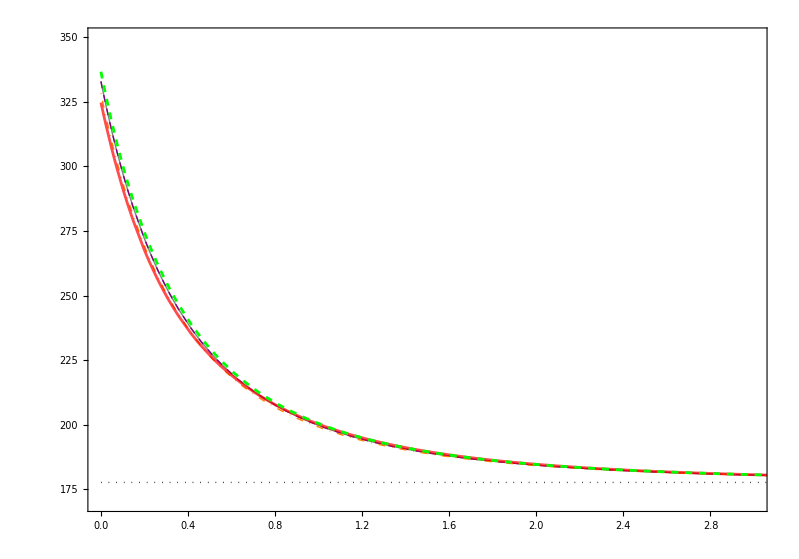

```mathematica
g1=Plot[{ Subscript[Δ, EdS][z],Subscript[Δ, ΛCDM][z], Subscript[Δ, neDE][z], Subscript[Δ, ESCVG][z], Subscript[Δ, 2FORM][z],Subscript[Δ, NA][z]}, {z,0,10},
Frame->True,Axes->False, ImageSize->5*350/3.54*{GoldenRatio,1}, AspectRatio->0.7,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->18, Bold},FrameLabel->(MaTeX[#,Magnification->3]&)/@{"\\boldsymbol{z}", "\\boldsymbol{\\Delta_{vir}(z)}"}, 
PlotStyle->{ Directive[Thick, Black, Dotted], 
Directive[Thick, Gray], 
Directive[Thick, Purple, Dashed], 
Directive[Thick, Orange, DotDashed], 
Directive[ Medium,Red, Opacity[0.7]], 
Directive[ Green, Dashing[Small]]}, 
PlotRange->{{0, 3},{170, 350}}, 
PlotLegends->Placed[LineLegend[{
Directive[Thick, Black, Dotted],
Directive[Thick, Gray],
Directive[Thick, Purple, Dashed],
Directive[Thick, Orange, DotDashed], 
Directive[ Medium,Red, Opacity[0.7]],
Directive[ Green, Dashing[Small]]}, 
{(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{EdS}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{\\Lambda CDM}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{neDE}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{EOCVG}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{2FORM}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{NA}"]}, 
LegendMarkerSize->30,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&), LegendLayout->{"Column",1},LabelStyle->{Black,Bold,15}],{{0.72,0.3},{0,0}}]]
```

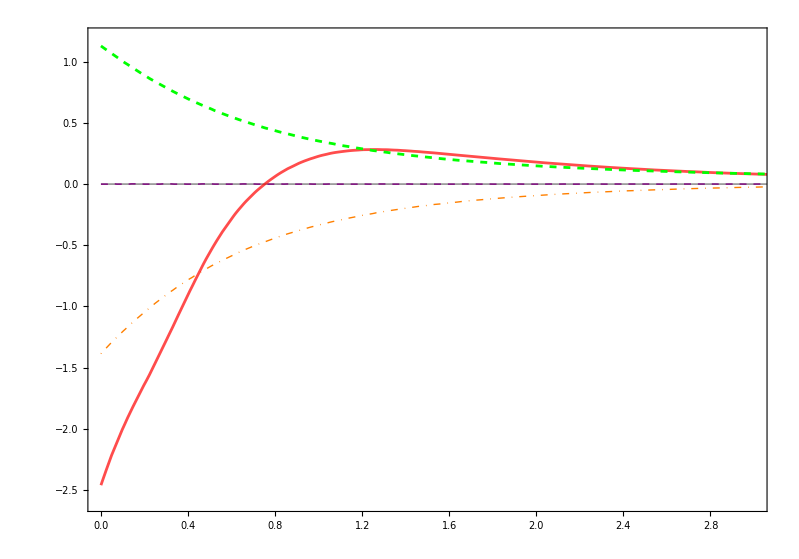

```mathematica
g2=Plot[{ ((Subscript[Δ, ΛCDM][z]-Subscript[Δ, ΛCDM][z])/Subscript[Δ, ΛCDM][z])*100, ((Subscript[Δ, neDE][z]-Subscript[Δ, ΛCDM][z])/Subscript[Δ, ΛCDM][z])*100,(( Subscript[Δ, ESCVG][z]-Subscript[Δ, ΛCDM][z])/Subscript[Δ, ΛCDM][z])*100, ((Subscript[Δ, 2FORM][z]-Subscript[Δ, ΛCDM][z])/Subscript[Δ, ΛCDM][z])*100,((Subscript[Δ, NA][z]-Subscript[Δ, ΛCDM][z])/Subscript[Δ, ΛCDM][z])*100}, {z,0,10},
Frame->True,Axes->False, ImageSize->5*350/3.54*{GoldenRatio,1}, AspectRatio->0.7,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->18, Bold},FrameLabel->(MaTeX[#,Magnification->3]&)/@{"\\boldsymbol{z}", "\\boldsymbol{\\Delta_{vir}(\\%)}"}, 
PlotStyle->{ 
Directive[Thick, Gray], 
Directive[Thick, Purple, Dashed], 
Directive[Thick, Orange, DotDashed], 
Directive[ Medium,Red, Opacity[0.7]], 
Directive[ Green, Dashing[Small]]}, 
PlotRange->{{0, 3},{-2.6, 1.2}}]
```

```mathematica
ResourceFunction["PlotGrid"][{{g1},{g2}}]
```

-Graphics-

## Densidad numérica, masa 10.b9⁴

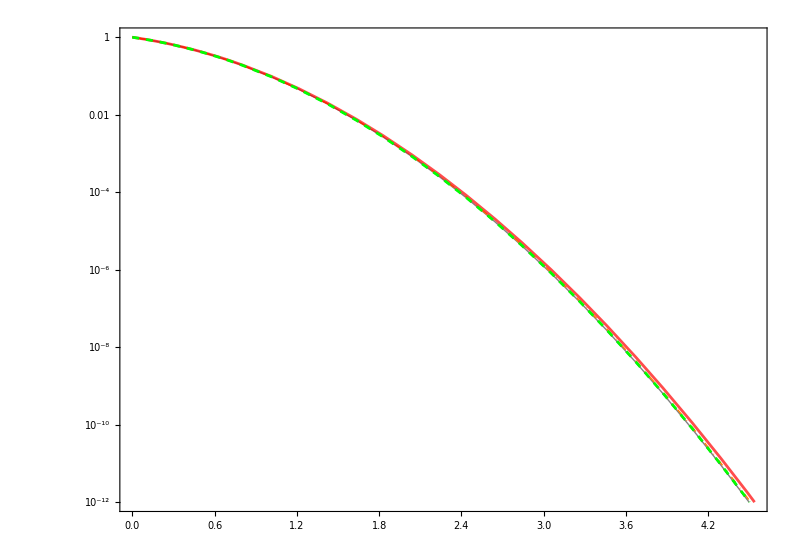

```mathematica
Plot[{ Subscript[dn, cΛCDM][z]/Subscript[dn, cΛCDM][0], Subscript[dn, cneDE][z]/Subscript[dn, cneDE][0], Subscript[dn, ESCVG][z]/Subscript[dn, ESCVG][0], Subscript[dn, 2FORM][z]/Subscript[dn, 2FORM][0],Subscript[dn, NA][z]/Subscript[dn, NA][0]}, {z,0,10},
Frame->True,Axes->False, ImageSize->5*350/3.54*{GoldenRatio,1},AspectRatio->0.7,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->18, Bold},FrameLabel->(MaTeX[#,Magnification->3]&)/@{"\\boldsymbol{z}", "\\boldsymbol{dn \\, / \\, dM}"}, 
PlotStyle->{  
Directive[Thick, Gray], 
Directive[Thick, Purple, Dashed], 
Directive[Thick, Orange, DotDashed], 
Directive[ Medium,Red, Opacity[0.7]], 
Directive[ Green, Dashing[Small]]}, 
PlotRange->{{0, 5},{5, 10^(-12)}}, 
PlotLegends->Placed[LineLegend[{
Directive[Thick, Gray],
Directive[Thick, Purple, Dashed],
Directive[Thick, Orange, DotDashed],
Directive[ Medium,Red, Opacity[0.7]],
Directive[ Green, Dashing[Small]]}, 
{(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{\\Lambda CDM}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{neDE}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{EOCVG}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{2FORM}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{NA}"]}, 
LegendMarkerSize->30,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&), LegendLayout->{"Column",1},LabelStyle->{Black,Bold,15}],{{0.72,0.42},{0,0}}], ScalingFunctions->"Log"]
```

## Elemento de volumen comóvil

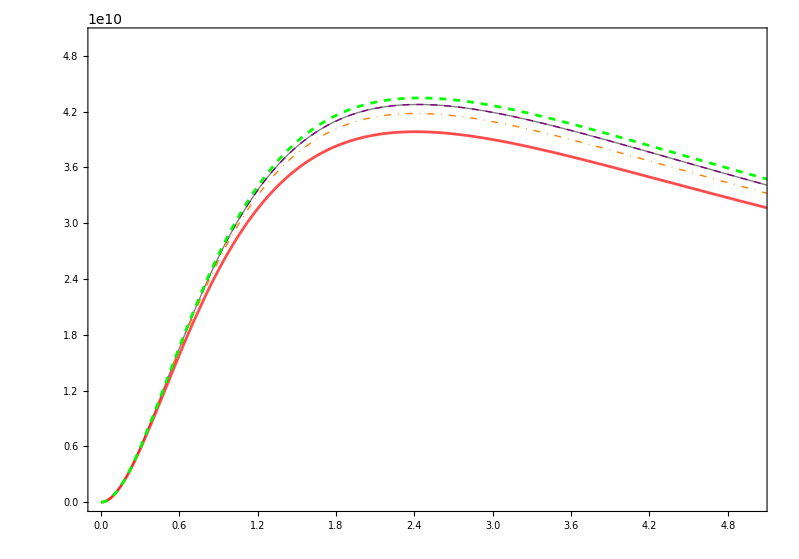

```mathematica
Plot[{ Subscript[V, cΛCDM][z], Subscript[V, cneDE][z], Subscript[V, cESCVG][z], Subscript[V, c2FORM][z], Subscript[V, cNA][z]}, {z,0,10},
Frame->True,Axes->False, ImageSize->5*350/3.54*{GoldenRatio,1}, AspectRatio->0.7,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->18, Bold},FrameLabel->(MaTeX[#,Magnification->3]&)/@{"\\boldsymbol{z}", "\\boldsymbol{dV \\, / \\, dz \\, d\\Omega}"}, 
PlotStyle->{Directive[Thick, Gray], 
Directive[Thick, Purple, Dashed], 
Directive[Thick, Orange, DotDashed], 
Directive[ Medium,Red, Opacity[0.7]], 
Directive[ Green, Dashing[Small]]}, 
PlotRange->{{0, 5},{0, 5*10^(10)}}, 
PlotLegends->Placed[LineLegend[{
Directive[Thick, Gray],
Directive[Thick, Purple, Dashed],
Directive[Thick, Orange, DotDashed],
Directive[ Medium,Red, Opacity[0.7]],
Directive[ Green, Dashing[Small]]}, 
{(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{\\Lambda CDM}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{neDE}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{EOCVG}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{2FORM}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{NA}"]}, 
LegendMarkerSize->30,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&), LegendLayout->{"Column",1},LabelStyle->{Black,Bold,15}],{{0.72,0.04},{0,0}}]]
```

## Número de halos, masa [10.b9.b3, 10.b9⁴]

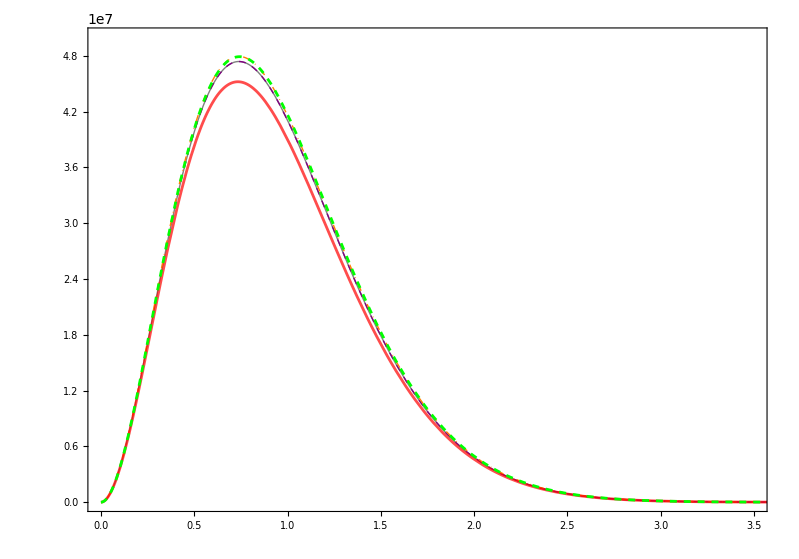

```mathematica
Plot[{Subscript[Nbin, cΛCDM][z], Subscript[Nbin, cneDE][z], Subscript[Nbin, cESCVG][z], Subscript[Nbin, c2FORM][z], Subscript[Nbin, cNA][z]}, {z,0,10},
Frame->True,Axes->False, ImageSize->5*350/3.54*{GoldenRatio,1}, AspectRatio->0.7,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->18, Bold},FrameLabel->(MaTeX[#,Magnification->3]&)/@{"\\boldsymbol{z}", "\\boldsymbol{\\mathcal{N}^{bin}}"}, 
PlotStyle->{ Directive[Thick, Gray], 
Directive[Thick, Purple, Dashed], 
Directive[Thick, Orange, DotDashed], 
Directive[ Medium,Red, Opacity[0.7]], 
Directive[ Green, Dashing[Small]]}, 
PlotRange->{{0, 3.5},{0, 5*10^(7)}}, 
PlotLegends->Placed[LineLegend[{
Directive[Thick, Gray], 
Directive[Thick, Purple, Dashed], 
Directive[Thick, Orange, DotDashed],
Directive[ Medium,Red, Opacity[0.7]],
Directive[ Green, Dashing[Small]]}, 
{(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{\\Lambda CDM}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{neDE}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{EOCVG}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{2FORM}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{NA}"]}, 
LegendMarkerSize->30,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&), LegendLayout->{"Column",1},LabelStyle->{Black,Bold,15}],{{0.72,0.4},{0,0}}]]
```

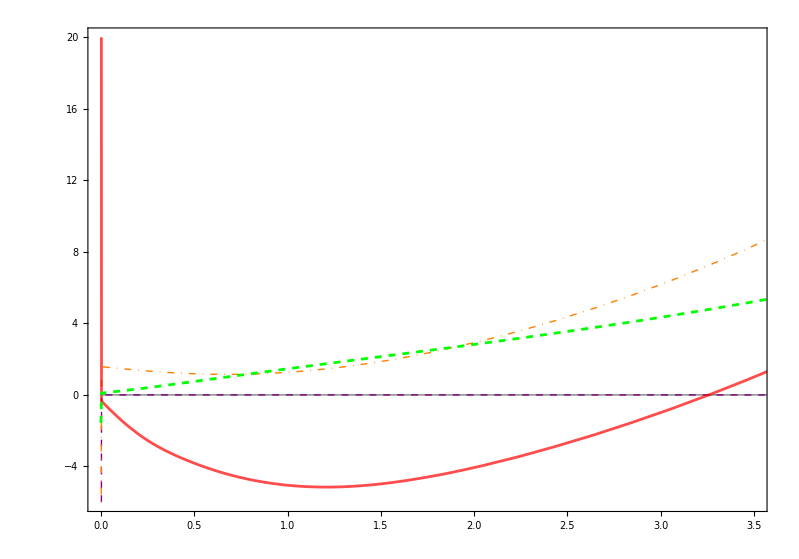

```mathematica
Plot[{((Subscript[Nbin, cΛCDM][z]-Subscript[Nbin, cΛCDM][z])/Subscript[Nbin, cΛCDM][z])*100, ((Subscript[Nbin, cneDE][z]-Subscript[Nbin, cΛCDM][z])/Subscript[Nbin, cΛCDM][z])*100,(( Subscript[Nbin, cESCVG][z]-Subscript[Nbin, cΛCDM][z])/Subscript[Nbin, cΛCDM][z])*100,(( Subscript[Nbin, c2FORM][z]-Subscript[Nbin, cΛCDM][z])/Subscript[Nbin, cΛCDM][z])*100,(( Subscript[Nbin, cNA][z]-Subscript[Nbin, cΛCDM][z])/Subscript[Nbin, cΛCDM][z])*100}, {z,0,10},
Frame->True,Axes->False, ImageSize->5*350/3.54*{GoldenRatio,1}, AspectRatio->0.7,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->18, Bold},FrameLabel->(MaTeX[#,Magnification->3]&)/@{"\\boldsymbol{z}", "\\boldsymbol{\\mathcal{N}^{bin}}"}, 
PlotStyle->{ Directive[Thick, Gray], 
Directive[Thick, Purple, Dashed], 
Directive[Thick, Orange, DotDashed], 
Directive[ Medium,Red, Opacity[0.7]], 
Directive[ Green, Dashing[Small]]}, 
PlotRange->{{0, 3.5},{-6, 20}}]
```

## Número de halos, masa [10.b9⁴, 10.b9⁵]

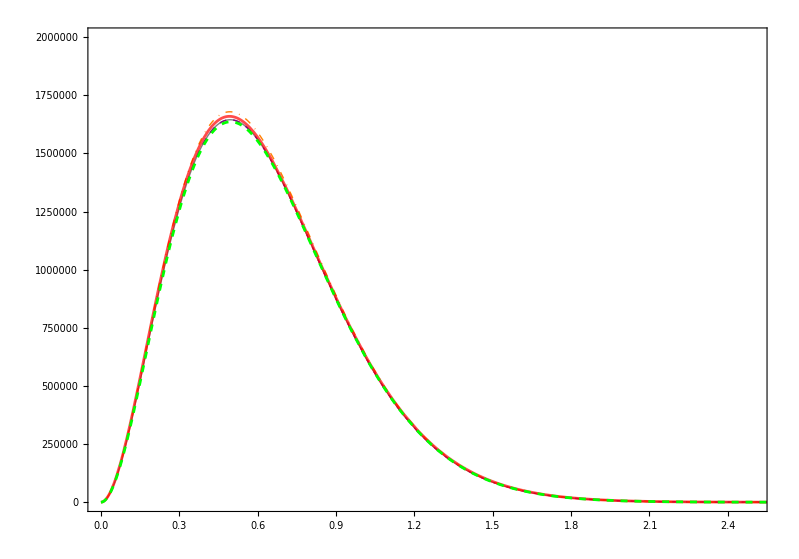

```mathematica
Plot[{ Subscript[Nbin, 2cΛCDM][z], Subscript[Nbin, 2cneDE][z], Subscript[Nbin, 2cESCVG][z], Subscript[Nbin, 2c2FORM][z], Subscript[Nbin, 2cNA][z]}, {z,0,10},
Frame->True,Axes->False, ImageSize->5*350/3.54*{GoldenRatio,1}, AspectRatio->0.7,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->18, Bold},FrameLabel->(MaTeX[#,Magnification->3]&)/@{"\\boldsymbol{z}", "\\boldsymbol{\\mathcal{N}^{bin}}"}, 
PlotStyle->{ Directive[Thick, Gray], 
Directive[Thick, Purple, Dashed], 
Directive[Thick, Orange, DotDashed], 
Directive[ Medium,Red, Opacity[0.7]], 
Directive[ Green, Dashing[Small]]}, 
PlotRange->{{0, 2.5},{0, 2*10^(6)}}(*, 
PlotLegends->Placed[LineLegend[{
Directive[Thick, Gray], 
Directive[Thick, Purple, Dashed],
Directive[Thick, Orange, DotDashed],
Directive[ Medium,Red, Opacity[0.7]],
Directive[ Green, Dashing[Small]]}, 
{(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{\\Lambda CDM}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{neDE}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{EOCVG}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{2FORM}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{NA}"]}, 
LegendMarkerSize->30,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&), LegendLayout->{"Column",1},LabelStyle->{Black,Bold,15}],{{0.72,0.4},{0,0}}]*)]
```

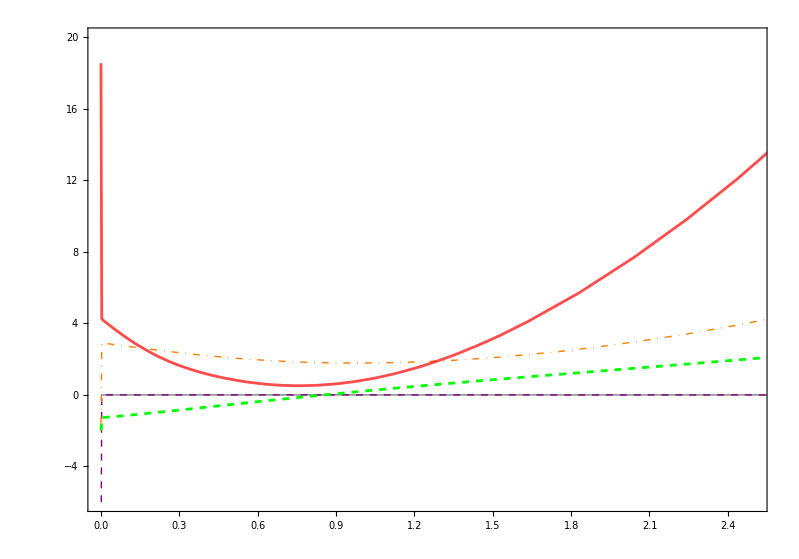

```mathematica
Plot[{((Subscript[Nbin, 2cΛCDM][z]-Subscript[Nbin, 2cΛCDM][z])/Subscript[Nbin, 2cΛCDM][z])*100, ((Subscript[Nbin, 2cneDE][z]-Subscript[Nbin, 2cΛCDM][z])/Subscript[Nbin, 2cΛCDM][z])*100,(( Subscript[Nbin, 2cESCVG][z]-Subscript[Nbin, 2cΛCDM][z])/Subscript[Nbin, 2cΛCDM][z])*100,(( Subscript[Nbin, 2c2FORM][z]-Subscript[Nbin, 2cΛCDM][z])/Subscript[Nbin, 2cΛCDM][z])*100,(( Subscript[Nbin, 2cNA][z]-Subscript[Nbin, 2cΛCDM][z])/Subscript[Nbin, 2cΛCDM][z])*100}, {z,0,10},
Frame->True,Axes->False, ImageSize->5*350/3.54*{GoldenRatio,1}, AspectRatio->0.7,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->18, Bold},FrameLabel->(MaTeX[#,Magnification->3]&)/@{"\\boldsymbol{z}", "\\boldsymbol{\\mathcal{N}^{bin}}"}, 
PlotStyle->{ Directive[Thick, Gray], 
Directive[Thick, Purple, Dashed], 
Directive[Thick, Orange, DotDashed], 
Directive[ Medium,Red, Opacity[0.7]], 
Directive[ Green, Dashing[Small]]}, 
PlotRange->{{0, 2.5},{-6, 20}}]
```

## Número de halos, masa [10.b9⁵, 10.b9⁶]

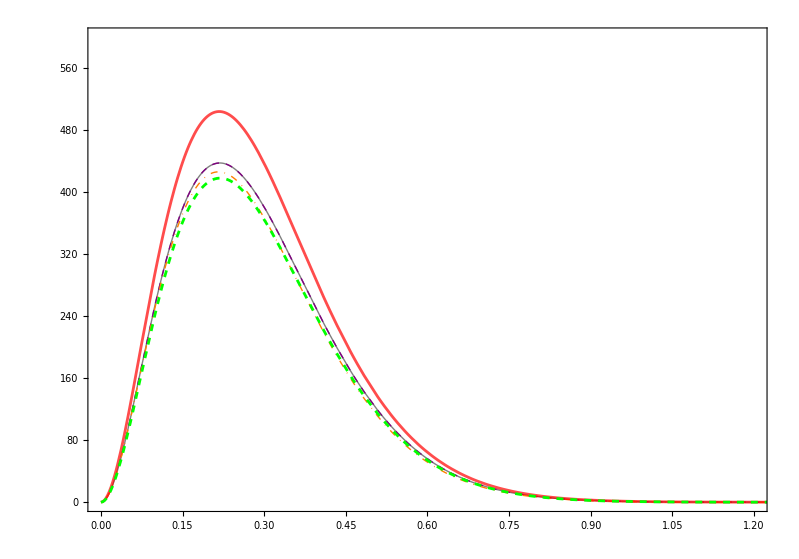

```mathematica
Plot[{ Subscript[Nbin, 3cΛCDM][z], Subscript[Nbin, 3cneDE][z], Subscript[Nbin, 3cESCVG][z], Subscript[Nbin, 3c2FORM][z], Subscript[Nbin, 3cNA][z]}, {z,0,10},
Frame->True,Axes->False, ImageSize->5*350/3.54*{GoldenRatio,1}, AspectRatio->0.7,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->18, Bold},FrameLabel->(MaTeX[#,Magnification->3]&)/@{"\\boldsymbol{z}", "\\boldsymbol{\\mathcal{N}^{bin}}"}, 
PlotStyle->{ Directive[Thick, Gray], 
Directive[Thick, Purple, Dashed], 
Directive[Thick, Orange, DotDashed], 
Directive[ Medium,Red, Opacity[0.7]], 
Directive[ Green, Dashing[Small]]}, 
PlotRange->{{0, 1.2},{0, 600}}(*, 
PlotLegends->Placed[LineLegend[{
Directive[Thick, Gray], 
Directive[Thick, Purple, Dashed],
Directive[Thick, Orange, DotDashed],
Directive[ Medium,Red, Opacity[0.7]],
Directive[ Green, Dashing[Small]]}, 
{(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{\\Lambda CDM}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{neDE}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{EOCVG}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{2FORM}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{NA}"]}, 
LegendMarkerSize->30,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&), LegendLayout->{"Column",1},LabelStyle->{Black,Bold,15}],{{0.72,0.4},{0,0}}]*)]
```

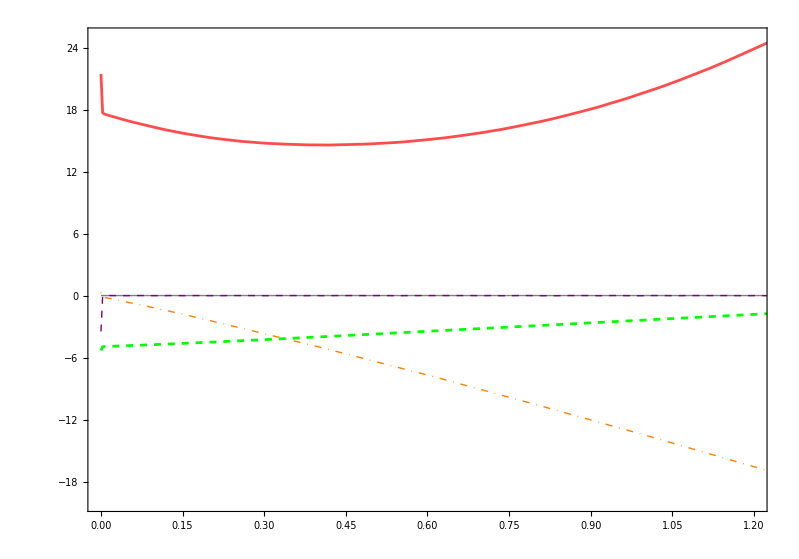

```mathematica
Plot[{((Subscript[Nbin, 3cΛCDM][z]-Subscript[Nbin, 3cΛCDM][z])/Subscript[Nbin, 3cΛCDM][z])*100, ((Subscript[Nbin, 3cneDE][z]-Subscript[Nbin, 3cΛCDM][z])/Subscript[Nbin, 3cΛCDM][z])*100,(( Subscript[Nbin, 3cESCVG][z]-Subscript[Nbin, 3cΛCDM][z])/Subscript[Nbin, 3cΛCDM][z])*100,(( Subscript[Nbin, 3c2FORM][z]-Subscript[Nbin, 3cΛCDM][z])/Subscript[Nbin, 3cΛCDM][z])*100,(( Subscript[Nbin, 3cNA][z]-Subscript[Nbin, 3cΛCDM][z])/Subscript[Nbin, 3cΛCDM][z])*100}, {z,0,10},
Frame->True,Axes->False, ImageSize->5*350/3.54*{GoldenRatio,1}, AspectRatio->0.7,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->18, Bold},FrameLabel->(MaTeX[#,Magnification->3]&)/@{"\\boldsymbol{z}", "\\boldsymbol{\\mathcal{N}^{bin}}"}, 
PlotStyle->{ Directive[Thick, Gray], 
Directive[Thick, Purple, Dashed], 
Directive[Thick, Orange, DotDashed], 
Directive[ Medium,Red, Opacity[0.7]], 
Directive[ Green, Dashing[Small]]}, 
PlotRange->{{0, 1.2},{-20, 25}}]
```

```mathematica
9
```

## Número de halos integrado, masa [10.b9.b3, 10.b9⁶]

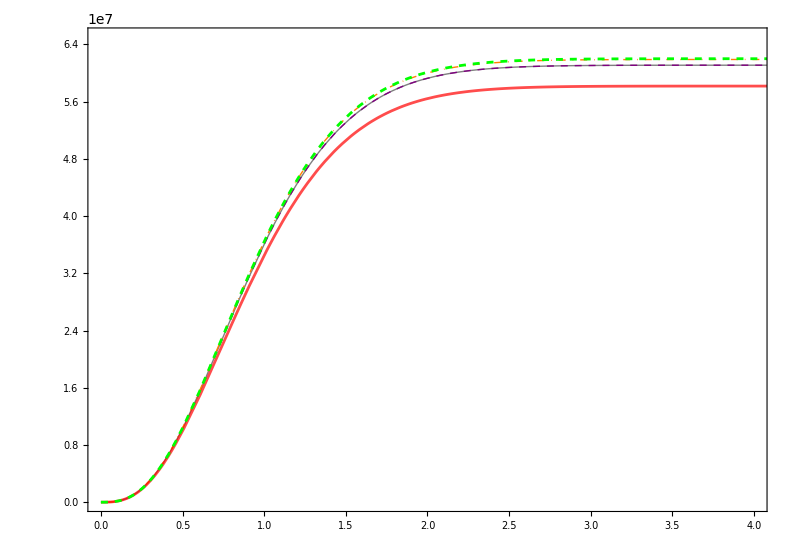

```mathematica
Plot[{ Subscript[Nsi, cΛCDM][z], Subscript[Nsi, cneDE][z], Subscript[Nsi, cESCVG][z], Subscript[Nsi, c2FORM][z], Subscript[Nsi, cNA][z]}, {z,0,10},
Frame->True,Axes->False, ImageSize->5*350/3.54*{GoldenRatio,1}, AspectRatio->0.7,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->18, Bold},FrameLabel->(MaTeX[#,Magnification->3]&)/@{"\\boldsymbol{z}", "\\boldsymbol{N}"}, 
PlotStyle->{ Directive[Thick, Gray], 
Directive[Thick, Purple, Dashed], 
Directive[Thick, Orange, DotDashed], 
Directive[ Medium,Red, Opacity[0.7]], 
Directive[ Green, Dashing[Small]]}, 
PlotRange->{{0, 4},{0,6.5*10^(7)}}, 
PlotLegends->Placed[LineLegend[{
Directive[Thick, Gray],
Directive[Thick, Purple, Dashed],
Directive[Thick, Orange, DotDashed],
Directive[ Medium,Red, Opacity[0.7]],
Directive[ Green, Dashing[Small]]}, 
{(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{\\Lambda CDM}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{neDE}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{EOCVG}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{2FORM}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{NA}"]}, 
LegendMarkerSize->30,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&), LegendLayout->{"Column",1},LabelStyle->{Black,Bold,15}],{{0.72,0.03},{0,0}}]]
```

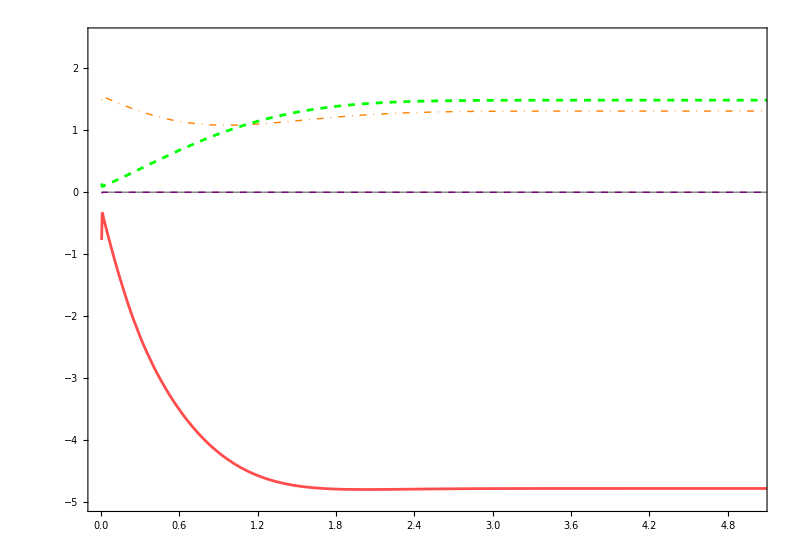

```mathematica
Plot[{((Subscript[Nsi, cΛCDM][z]-Subscript[Nsi, cΛCDM][z])/Subscript[Nsi, cΛCDM][z])*100, ((Subscript[Nsi, cneDE][z]-Subscript[Nsi, cΛCDM][z])/Subscript[Nsi, cΛCDM][z])*100,(( Subscript[Nsi, cESCVG][z]-Subscript[Nsi, cΛCDM][z])/Subscript[Nsi, cΛCDM][z])*100,(( Subscript[Nsi, c2FORM][z]-Subscript[Nsi, cΛCDM][z])/Subscript[Nsi, cΛCDM][z])*100,(( Subscript[Nsi, cNA][z]-Subscript[Nsi, cΛCDM][z])/Subscript[Nsi, cΛCDM][z])*100}, {z,0,10},
Frame->True,Axes->False, ImageSize->5*350/3.54*{GoldenRatio,1}, AspectRatio->0.7,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->18, Bold},FrameLabel->(MaTeX[#,Magnification->3]&)/@{"\\boldsymbol{z}", "\\boldsymbol{\\mathcal{N}^{bin}}"}, 
PlotStyle->{ Directive[Thick, Gray], 
Directive[Thick, Purple, Dashed], 
Directive[Thick, Orange, DotDashed], 
Directive[ Medium,Red, Opacity[0.7]], 
Directive[ Green, Dashing[Small]]}, 
PlotRange->{{0, 5},{-5, 2.5}}]
```

## Número de halos integrado, masa [10.b9⁴, 10.b9⁶]

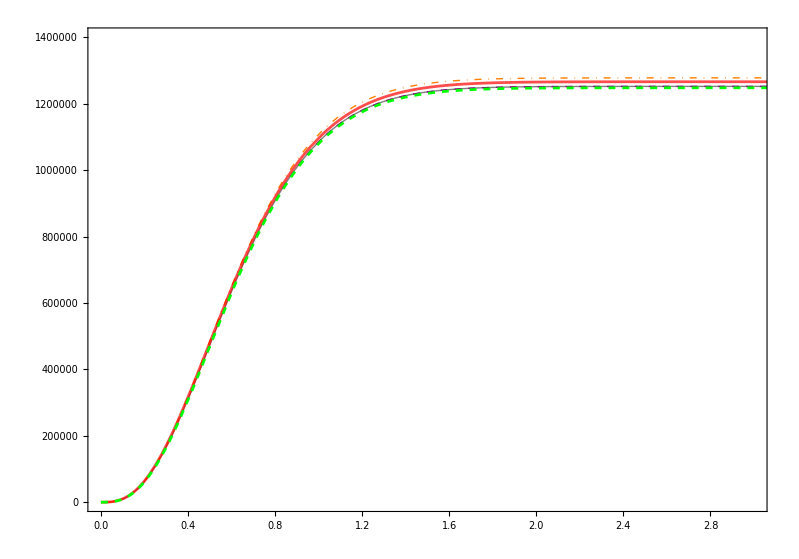

```mathematica
Plot[{ Subscript[Nsi, 2cΛCDM][z], Subscript[Nsi, 2cneDE][z], Subscript[Nsi, 2cESCVG][z], Subscript[Nsi, 2c2FORM][z], Subscript[Nsi, 2cNA][z]}, {z,0,10},
Frame->True,Axes->False, ImageSize->5*350/3.54*{GoldenRatio,1}, AspectRatio->0.7,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->20, Bold},FrameLabel->(MaTeX[#,Magnification->3]&)/@{"\\boldsymbol{z}", "\\boldsymbol{N}"}, 
PlotStyle->{ Directive[Thick, Gray], 
Directive[Thick, Purple, Dashed], 
Directive[Thick, Orange, DotDashed], 
Directive[ Medium,Red, Opacity[0.7]], 
Directive[ Green, Dashing[Small]]}, 
PlotRange->{{0, 3},{0,1.4*10^(6)}}(*, 
PlotLegends->Placed[LineLegend[{
Directive[Thick, Gray],
Directive[Thick, Purple, Dashed],
Directive[Thick, Orange, DotDashed],
Directive[ Medium,Red, Opacity[0.7]],
Directive[ Green, Dashing[Small]]}, 
{(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{\\Lambda CDM}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{neDE}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{EOCVG}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{2FORM}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{NA}"]}, 
LegendMarkerSize->30,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&), LegendLayout->{"Column",1},LabelStyle->{Black,Bold,15}],{{0.72,0.03},{0,0}}]*)]
```

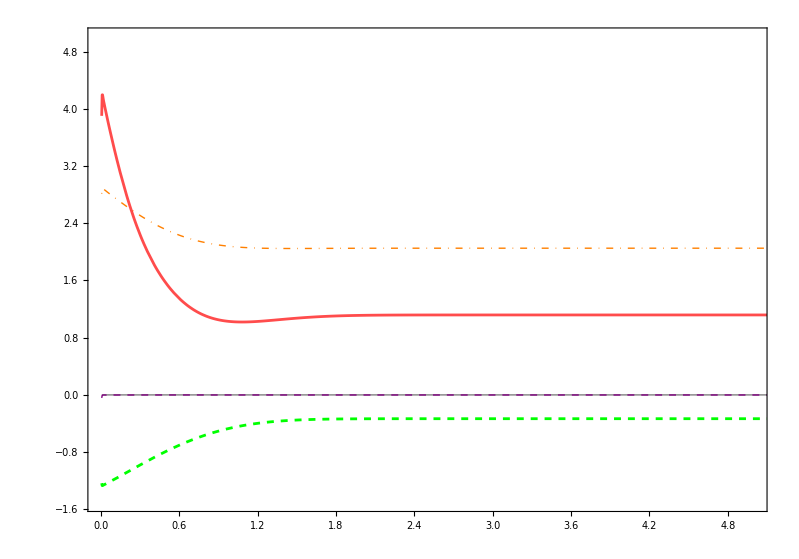

```mathematica
Plot[{((Subscript[Nsi, 2cΛCDM][z]-Subscript[Nsi, 2cΛCDM][z])/Subscript[Nsi, 2cΛCDM][z])*100, ((Subscript[Nsi, 2cneDE][z]-Subscript[Nsi, 2cΛCDM][z])/Subscript[Nsi, 2cΛCDM][z])*100,(( Subscript[Nsi, 2cESCVG][z]-Subscript[Nsi, 2cΛCDM][z])/Subscript[Nsi, 2cΛCDM][z])*100,(( Subscript[Nsi, 2c2FORM][z]-Subscript[Nsi, 2cΛCDM][z])/Subscript[Nsi, 2cΛCDM][z])*100,(( Subscript[Nsi, 2cNA][z]-Subscript[Nsi, 2cΛCDM][z])/Subscript[Nsi, 2cΛCDM][z])*100}, {z,0,10},
Frame->True,Axes->False, ImageSize->5*350/3.54*{GoldenRatio,1}, AspectRatio->0.7,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->18, Bold},FrameLabel->(MaTeX[#,Magnification->3]&)/@{"\\boldsymbol{z}", "\\boldsymbol{\\mathcal{N}^{bin}}"}, 
PlotStyle->{ Directive[Thick, Gray], 
Directive[Thick, Purple, Dashed], 
Directive[Thick, Orange, DotDashed], 
Directive[ Medium,Red, Opacity[0.7]], 
Directive[ Green, Dashing[Small]]}, 
PlotRange->{{0, 5},{-1.5, 5}}]
```

## Número de halos integrado, masa [10.b9⁵, 10.b9⁶]

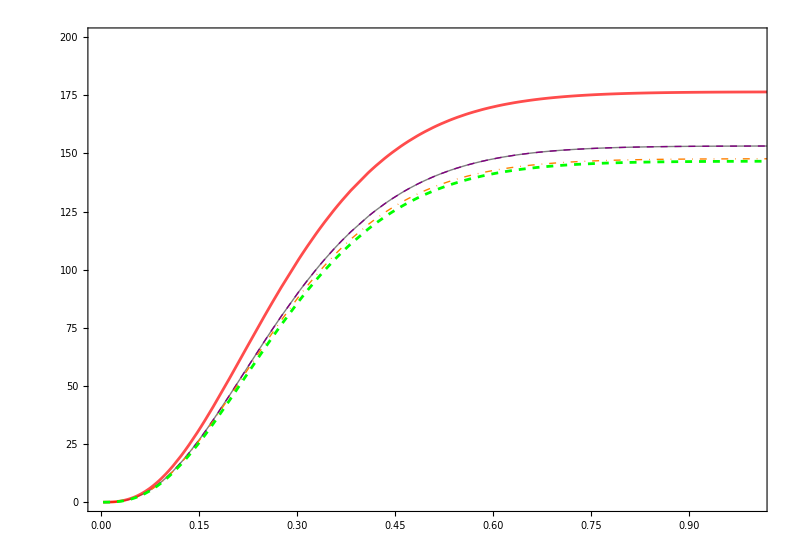

```mathematica
Plot[{ Subscript[Nsi, 3cΛCDM][z], Subscript[Nsi, 3cneDE][z], Subscript[Nsi, 3cESCVG][z],Subscript[Nsi, 3c2FORM][z],Subscript[Nsi, 3cNA][z]}, {z,0,10},
Frame->True,Axes->False, ImageSize->5*350/3.54*{GoldenRatio,1}, AspectRatio->0.7,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->20, Bold},FrameLabel->(MaTeX[#,Magnification->3]&)/@{"\\boldsymbol{z}", "\\boldsymbol{N}"}, 
PlotStyle->{ Directive[Thick, Gray], 
Directive[Thick, Purple, Dashed], 
Directive[Thick, Orange, DotDashed], 
Directive[ Medium,Red, Opacity[0.7]], 
Directive[ Green, Dashing[Small]]}, 
PlotRange->{{0, 1},{0,200}}(*, 
PlotLegends->Placed[LineLegend[{
Directive[Thick, Gray],
Directive[Thick, Purple, Dashed],
Directive[Thick, Orange, DotDashed],
Directive[ Medium,Red, Opacity[0.7]],
Directive[ Green, Dashing[Small]]}, 
{(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{\\Lambda CDM}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{neDE}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{EOCVG}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{2FORM}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\boldsymbol{NA}"]}, 
LegendMarkerSize->30,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&), LegendLayout->{"Column",1},LabelStyle->{Black,Bold,15}],{{0.72,0.03},{0,0}}]*)]
```

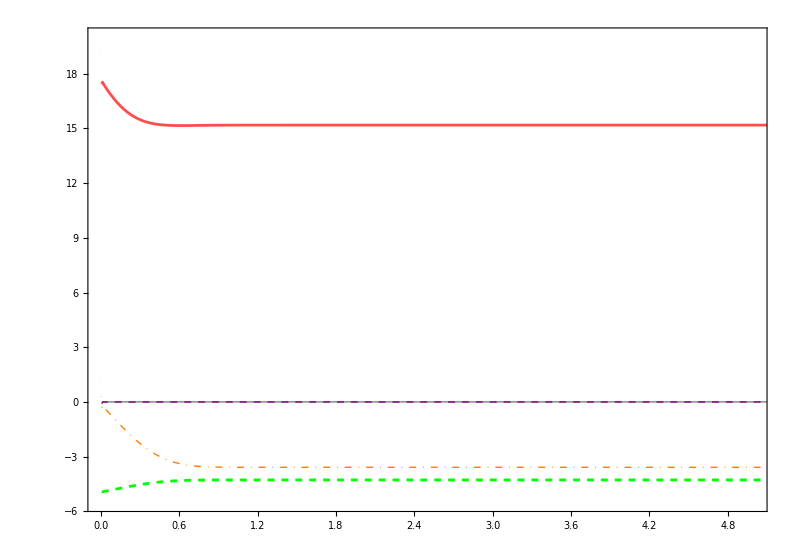

```mathematica
Plot[{((Subscript[Nsi, 3cΛCDM][z]-Subscript[Nsi, 3cΛCDM][z])/Subscript[Nsi, 3cΛCDM][z])*100, ((Subscript[Nsi, 3cneDE][z]-Subscript[Nsi, 3cΛCDM][z])/Subscript[Nsi, 3cΛCDM][z])*100,(( Subscript[Nsi, 3cESCVG][z]-Subscript[Nsi, 3cΛCDM][z])/Subscript[Nsi, 3cΛCDM][z])*100,(( Subscript[Nsi, 3c2FORM][z]-Subscript[Nsi, 3cΛCDM][z])/Subscript[Nsi, 3cΛCDM][z])*100,(( Subscript[Nsi, 3cNA][z]-Subscript[Nsi, 3cΛCDM][z])/Subscript[Nsi, 3cΛCDM][z])*100}, {z,0,10},
Frame->True,Axes->False, ImageSize->5*350/3.54*{GoldenRatio,1}, AspectRatio->0.7,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->18, Bold},FrameLabel->(MaTeX[#,Magnification->3]&)/@{"\\boldsymbol{z}", "\\boldsymbol{\\mathcal{N}^{bin}}"}, 
PlotStyle->{ Directive[Thick, Gray], 
Directive[Thick, Purple, Dashed], 
Directive[Thick, Orange, DotDashed], 
Directive[ Medium,Red, Opacity[0.7]], 
Directive[ Green, Dashing[Small]]}, 
PlotRange->{{0, 5},{-5.5, 20}}]
```

## Función para crear gráficos

```mathematica
CrearGrafico[funciones_List,rango_,etiquetaEjeX_,etiquetaEjeY_, rangoEjeX_,rangoEjeY_, aspecto_, posicionLegenda_]:=Plot[funciones,rango,
Frame->True,Axes->False, ImageSize->5*350/3.54*{GoldenRatio,1},AspectRatio->aspecto,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->18},
 FrameLabel->(MaTeX[#,Magnification->2]&)/@{etiquetaEjeX, etiquetaEjeY},
PlotStyle->{ Directive[Thick, Black], 
Directive[Thick, Gray]}, 
PlotRange->{rangoEjeX,rangoEjeY}, 
PlotLegends->Placed[LineLegend[{
Directive[Thick, Black],
Directive[Thick, Gray]}, 
{(MaTeX[#,Magnification->1.3]&)/@Style["Sin"],
(MaTeX[#,Magnification->1.3]&)/@Style["Cos"]}, 
LegendMarkerSize->25,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&), LegendLayout->{"Column",1},LabelStyle->{Black,Bold,12}],{posicionLegenda,{0,0}}]]
```

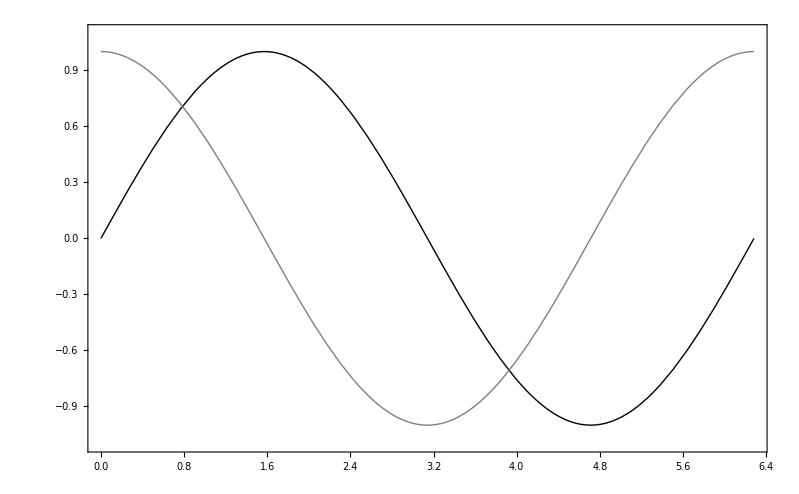

```mathematica
CrearGrafico[{Sin[x],Cos[x]},{x,0,2 Pi},"z","Eje Y",{0, 2 Pi}, {-1.1,1.1}, Full, {0.6,0.7}]
```